## Preamble

```mathematica
SetDirectory[NotebookDirectory[]]
dir="tables\\";
```

```mathematica
color1=Darker[RGBColor[65/255,144/255,210/255],.15]
color2=RGBColor[138/255,32/255,13/255]
color3=RGBColor[65/255,144/255,10/255]
color4=Darker[Orange,.1];
```

RGBColor[0.21666666666666665, 0.48, 0.7]

RGBColor[Rational[46, 85], Rational[32, 255], Rational[13, 255]]

RGBColor[Rational[13, 51], Rational[48, 85], Rational[2, 51]]

```mathematica
FPR=100/10000;
FNR=152/1000;
```

```mathematica
(* Mean of beta distrib. = α / (α+β) *)
gauss[x_,μ_,σ_]:=1/(√(2π)σ)Exp[-1/2((x-μ)/σ)^2];
binom[p_,ntot_,nyes_]:=(ntot+1)Binomial[ntot,nyes] Exp[nyes Log[p]+(ntot-nyes) Log[1-p]];
beta[p_,α_?NumericQ,β_?NumericQ]:=((1-p)^(-1+β) p^(-1+α))/Beta[α,β];
Clear[α,β]
sol=Solve[α/(α+β)==μ&&(α β)/((α+β)^2(α+β+1))==V,{α,β}]
α=ny+1;β=nt-ny+1;
α=ny(1-FPR)+1;β=nt(1-FNR-FPR)-ny(1-FPR)+1;
α=ny+1;β=nt(1-FNR-FPR)-ny+1;
meani[ny_,nt_]=Simplify[α/(α+β)]
vari[ny_,nt_]=Simplify[(α β)/((α+β)^2(α+β+1))]
newmeanvari3[ny_,nt_]:=Module[{norm,mean,var,wprec=39},
post[p_]:=(nt+1)Binomial[nt,ny] Exp[ny Log[p]+(nt-ny) Log[1-p]];
jacob=(1-FNR-FPR);
postcorr[ptrue_]:=jacob post[pobs[ptrue]];
norm=NIntegrate[postcorr[p],{p,0,1},WorkingPrecision->wprec];
postcorr[p_]=postcorr[p]/norm;
mean=NIntegrate[x postcorr[x],{x,0,1},WorkingPrecision->wprec];
var=NIntegrate[x^2  postcorr[x],{x,0,1},WorkingPrecision->wprec]-mean^2;
{mean,var}
];
μvarfun[α_?NumericQ,β_?NumericQ]:=Module[{norm,μ,var,pmax=1/2},norm=1/NIntegrate[beta[p-p0,α,β],{p,0,pmax},WorkingPrecision->25];μ=norm NIntegrate[p beta[p-p0,α,β],{p,0,pmax},WorkingPrecision->25];
var=norm NIntegrate[p^2 beta[p-p0,α,β],{p,0,pmax},WorkingPrecision->25]-μ^2;
{μ,var}]
μvarfunhiprec[α_?NumericQ,β_?NumericQ]:=Module[{norm,μ,var,pmax=1/2},norm=1/NIntegrate[beta[p-p0,α,β],{p,0,pmax},WorkingPrecision->40];μ=norm NIntegrate[p beta[p-p0,α,β],{p,0,pmax},WorkingPrecision->40];
var=norm NIntegrate[p^2 beta[p-p0,α,β],{p,0,pmax},WorkingPrecision->40]-μ^2;
{μ,var}]
(*NIntegrate[gauss[x,.3,.03],{x,0,1}]
NIntegrate[binom[x,250,22],{x,0,1}]*)
```

{{α→(-V μ+μ^2-μ^3)/V,β→((-1+μ) (V-μ+μ^2))/V}}

(1+ny)/(2+(419 nt)/500)

((1+(419 nt)/500-ny) (1+ny))/((2+(419 nt)/500)^2 (3+(419 nt)/500))

{-5/419,1}

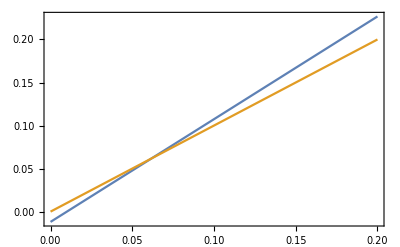

```mathematica
(* pobs -> prob. of observing a positive IgG/IgM result *)
(* ptrue -> prob. the tested person truly has the antibodies *)
pobs[ptrue_]:=ptrue(1-FNR-FPR)+FPR;
ptrue[pobs_]:=(pobs-FPR)/(1-FNR-FPR);
{p0=ptrue[0],ptrue[1-FNR]}
Plot[{ptrue[pobs],pobs},{pobs,0,.2},Frame->True]
```

### P2σfun

```mathematica
(* from old Round 1 *)
Clear[p2σstatesfun]
p2σstatesfun[post_,naivep_,minp_,maxp_]:=Module[{wprec=27},
{minpshort,maxpshort}={minp,Max[-3p0,naivep+(maxp-naivep)/3.]};
maxvalue=FindMaxValue[post[p],{p,Max[naivep,minpshort],minpshort,maxpshort},PrecisionGoal->4,AccuracyGoal->5,WorkingPrecision->wprec];
pmax=p/.FindMaximum[post[p],{p,Max[naivep,minpshort],minpshort,maxpshort},PrecisionGoal->4,AccuracyGoal->5,WorkingPrecision->wprec][[2]];
If[pmax==minpshort&&minpshort≠minp,Print["Error: minpshort too high! minpshort = "<>ToString[1.minpshort]]];
conflevel[pcut_]:=NIntegrate[post[p]HeavisideTheta[post[p]-pcut],{p,minp,maxp},Method->"LocalAdaptive",PrecisionGoal->4,AccuracyGoal->4,WorkingPrecision->wprec];
medianfun[x_?NumericQ]:=NIntegrate[post[p],{p,minp,x},Method->"LocalAdaptive",WorkingPrecision->wprec+5,PrecisionGoal->4,AccuracyGoal->4];
pmedian=x/.FindRoot[medianfun[x]==1/2,{x,(105/100)pmax},WorkingPrecision->wprec+5];
pcutvec=Range[maxvalue/100,maxvalue*5/10,maxvalue/90];
conffun=Interpolation[ParallelMap[{#,conflevel[#]}&,pcutvec]];
(*FindMinimum[(conffun[x]-0.95)^2,{x,3}]*)
pcut=x/.FindRoot[conffun[x]==95/100,{x,(1/10)conffun[[1,1,2]]},WorkingPrecision->wprec];
p2σmin=If[pmax==minp,minp,p/.FindRoot[post[p]==pcut,{p,Max[minp,(8/10)pmax],minp,pmax},WorkingPrecision->wprec]];
p2σmax=p/.FindRoot[post[p]==pcut,{p,(12/10)pmax,pmax,maxp},WorkingPrecision->wprec];
crosstest=NIntegrate[post[p],{p,p2σmin,p2σmax},WorkingPrecision->wprec,AccuracyGoal->5,PrecisionGoal->4];
If[crosstest>.955||crosstest<.945,Print["Error: 95% confidence level cross-check failed!"]];
{pmax,pmedian,p2σmin,p2σmax}+=p0; (* displacement due to FPR *)
(*pmax=Max[pmax,0];p2σmin=Max[p2σmin,0];*)
Print[Round[{pmax,p2σmin,p2σmax,crosstest},10.^-4]];
{pmax,pmedian,p2σmin,p2σmax,crosstest}
];
```

```mathematica
p2σstatesexactfun[post_,naivep_,minp_,maxp_]:=Module[{wprec=27},
{minpshort,maxpshort}={minp,naivep+(maxp-naivep)/3.};
maxvalue=FindMaxValue[post[p],{p,Max[naivep,minpshort],minpshort,maxpshort},PrecisionGoal->4,AccuracyGoal->5,WorkingPrecision->wprec];
pmax=p/.FindMaximum[post[p],{p,Max[naivep,minpshort],minpshort,maxpshort},PrecisionGoal->4,AccuracyGoal->5,WorkingPrecision->wprec][[2]];
If[pmax==minpshort&&minpshort≠minp,Print["Error: minpshort too high! minpshort = "<>ToString[1.minpshort]]];
conflevel[pcut_]:=NIntegrate[post[p]HeavisideTheta[post[p]-pcut],{p,minp,maxp},Method->"LocalAdaptive",PrecisionGoal->4,AccuracyGoal->4,WorkingPrecision->wprec];
medianfun[x_?NumericQ]:=NIntegrate[post[p],{p,minp,x},Method->"LocalAdaptive",WorkingPrecision->wprec+5,PrecisionGoal->4,AccuracyGoal->4];
pmedian=x/.FindRoot[medianfun[x]==1/2,{x,(107/100)pmax+10^-5},WorkingPrecision->wprec+5];
(*pmedian=1;*)
pcutvec=Range[maxvalue/100,maxvalue*5/10,maxvalue/90];
conffun=Interpolation[ParallelMap[{#,conflevel[#]}&,pcutvec]];
(*FindMinimum[(conffun[x]-0.95)^2,{x,3}]*)
pcut=x/.FindRoot[conffun[x]==95/100,{x,(1/10)conffun[[1,1,2]]},WorkingPrecision->wprec];
p2σmin=If[pmax==minp,minp,p/.NMinimize[{(finalpost2[p]-pcut)^2,minp<p<pmax},p,WorkingPrecision->wprec][[2]]];
p2σmax=p/.NMinimize[{(finalpost2[p]-pcut)^2,3/4>p>pmax},p,WorkingPrecision->wprec][[2]];
crosstest=NIntegrate[post[p],{p,p2σmin,p2σmax},WorkingPrecision->wprec,AccuracyGoal->5,PrecisionGoal->4];
If[crosstest>.954||crosstest<.946,Print["Error: 95% confidence level cross-check failed!"]];
(*pmax=Max[pmax,0];p2σmin=Max[p2σmin,0];*)
Print[Round[{pmax,pmedian,p2σmin,p2σmax,crosstest},10.^-4]];
{pmax,pmedian,p2σmin,p2σmax,crosstest}
];
```

```mathematica
errorfun[ptab_]:=Module[{},
Table[
pmode=ptab[[i,1]];
δplusminus={pmode-ptab[[i,3]],ptab[[i,4]]-pmode};
Around[100pmode,100δplusminus]
,{i,1,Length[ptab]}]
]
errormedianfun[ptab_]:=Module[{},
Table[
pmedian=ptab[[i,2]];
δplusminus={pmedian-ptab[[i,3]],ptab[[i,4]]-pmedian};
Around[100pmedian,100δplusminus]
,{i,1,Length[ptab]}]
]
```

```mathematica
(* Allows up to 500 cities *)
pname=Table[ToExpression["p"<>ToString[i]],{i,500}];
```

#### Exp issue

```mathematica
(*(compiledExp[x_Integer]:= #[x])& @ Compile[{{x, _Integer}},Exp[x]];*)
(compiledExp[x_Real]:= #[x])& @ Compile[{{x, _Real}},Exp[x]];
(compiledExp[x_Complex]:= #[x])& @ Compile[{{x, _Complex}},Exp[x]];

bigExp[x_?MachineNumberQ]:= Exp[SetPrecision[x,$MachinePrecision]];

munderflowExp[x_]:=
With[{y=compiledExp[x] (* Machine evaluation *)},
If[
y==0 (* Condition for machine underflow *),
bigExp[x] (* Action to take on machine underflow converting to a bignum result *),
y (* Machine precision result when underflow does not occur *)
]
];

Unprotect[Exp];
Exp[x_?MachineNumberQ]:=munderflowExp[x];
Protect[Exp];

Log[Exp[-1000]]
Log[Exp[-1000.]]
```

-1000

-1000.

## Main Calculations - 1st round

```mathematica
CloseKernels[];
LaunchKernels[10];
```

```mathematica
datacities=datacities3rounds[[All,{1,2,3,6,-1}]];
```

### Combining states

```mathematica
datacities[[All,1]]
(*statesindex={1,3,5,9,11,15,19,20,23,28,31,39,41,42,48,49,54,60,63,64,65,66,74,80,82,88,91}*)
statesindex={1,3,5,9,11,21,27,28,32,38,43,56,59,64,71,75,79,85,91,96,99,101,103,111,118,120,131,134};
datastates=Table[datacities[[statesindex[[i]];;(statesindex[[i+1]]-1)]],{i,Length[statesindex]-1}];
statesnames=datastates[[All,1,1]]
Dimensions[datastates]
datastates[[All,1,1]]
datastates[[1;;5]]
ncities=Table[Length[datastates[[i]]],{i,Length[datastates]}]
ilist=Flatten[Position[ncities,n_ /; n<5],1]
```

{AC,AC,AL,AL,AM,AM,AM,AM,AP,AP,BA,BA,BA,BA,BA,BA,BA,BA,BA,BA,CE,CE,CE,CE,CE,CE,DF,ES,ES,ES,ES,GO,GO,GO,GO,GO,GO,MA,MA,MA,MA,MA,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MS,MS,MS,MT,MT,MT,MT,MT,PA,PA,PA,PA,PA,PA,PA,PB,PB,PB,PB,PE,PE,PE,PE,PI,PI,PI,PI,PI,PI,PR,PR,PR,PR,PR,PR,RJ,RJ,RJ,RJ,RJ,RN,RN,RN,RO,RO,RR,RR,RS,RS,RS,RS,RS,RS,RS,RS,SC,SC,SC,SC,SC,SC,SC,SE,SE,SP,SP,SP,SP,SP,SP,SP,SP,SP,SP,SP,TO,TO,TO}

{AC,AL,AM,AP,BA,CE,DF,ES,GO,MA,MG,MS,MT,PA,PB,PE,PI,PR,RJ,RN,RO,RR,RS,SC,SE,SP,TO}

{27}

{AC,AL,AM,AP,BA,CE,DF,ES,GO,MA,MG,MS,MT,PA,PB,PE,PI,PR,RJ,RN,RO,RR,RS,SC,SE,SP,TO}

{{{AC,CRUZEIRO DO SUL,250,1,88376},{AC,RIO BRANCO,250,12,407319}},{{AL,ARAPIRACA,223,0,231747},{AL,MACEIÓ,234,3,1018948}},{{AM,LÁBREA,250,0,46069},{AM,MANAUS,250,27,2182763},{AM,PARINTINS,250,11,114273},{AM,TEFÉ,250,42,59849}},{{AP,MACAPÁ,250,21,503327},{AP,OIAPOQUE,250,8,27270}},{{BA,BARREIRAS,250,0,155439},{BA,FEIRA DE SANTANA,66,1,614872},{BA,GUANAMBI,245,0,84481},{BA,IRECÊ,41,0,72967},{BA,ITABUNA,60,0,213223},{BA,JUAZEIRO,250,0,216707},{BA,PAULO AFONSO,66,0,117782},{BA,SALVADOR,250,0,2872347},{BA,SANTO ANTÔNIO DE JESUS,86,0,101512},{BA,VITÓRIA DA CONQUISTA,86,0,338480}}}

{2,2,4,2,10,6,1,4,6,5,13,3,5,7,4,4,6,6,5,3,2,2,8,7,2,11,3}

{1,2,3,4,7,8,12,15,16,20,21,22,25,27}

```mathematica
Total[datastates[[All,All,3]],{2}]
totround1=Total[%]
```

{500,457,1000,500,1400,1064,240,746,1305,894,2328,606,327,1513,272,371,1236,1459,866,372,423,401,1985,1631,500,1898,731}

25025

```mathematica
datastates2=datastates;
Table[datastates2[[i]]=Cases[datastates[[i]],_?( GreaterEqual[#[[3]],mintot]&)],{i,Length[datastates]}];
ncities2=Table[Length[datastates2[[i]]],{i,Length[datastates2]}]
Total[datastates2[[All,All,3]],{2}]
Total[%]
```

{2,2,4,2,4,4,1,3,5,3,8,2,1,6,0,1,5,6,3,1,1,1,8,6,2,6,3}

{500,457,1000,500,995,949,240,722,1128,750,1972,493,208,1479,0,240,1236,1459,689,229,250,250,1985,1439,500,1381,731}

21782

```mathematica
datastates//TableForm
```

AC
CRUZEIRO DO SUL
250
1
88376 | AC
RIO BRANCO
250
12
407319 |  |  |  |  |  |  |  |  |  |  | 
AL
ARAPIRACA
223
0
231747 | AL
MACEIÓ
234
3
1018948 |  |  |  |  |  |  |  |  |  |  | 
AM
LÁBREA
250
0
46069 | AM
MANAUS
250
27
2182763 | AM
PARINTINS
250
11
114273 | AM
TEFÉ
250
42
59849 |  |  |  |  |  |  |  |  | 
AP
MACAPÁ
250
21
503327 | AP
OIAPOQUE
250
8
27270 |  |  |  |  |  |  |  |  |  |  | 
BA
BARREIRAS
250
0
155439 | BA
FEIRA DE SANTANA
66
1
614872 | BA
GUANAMBI
245
0
84481 | BA
IRECÊ
41
0
72967 | BA
ITABUNA
60
0
213223 | BA
JUAZEIRO
250
0
216707 | BA
PAULO AFONSO
66
0
117782 | BA
SALVADOR
250
0
2872347 | BA
SANTO ANTÔNIO DE JESUS
86
0
101512 | BA
VITÓRIA DA CONQUISTA
86
0
338480 |  |  | 
CE
CRATEÚS
247
2
75074 | CE
FORTALEZA
225
17
2669342 | CE
IGUATU
9
0
102498 | CE
JUAZEIRO DO NORTE
106
0
274207 | CE
QUIXADÁ
245
0
87728 | CE
SOBRAL
232
4
208935 |  |  |  |  |  |  | 
DF
BRASÍLIA
240
0
3015268 |  |  |  |  |  |  |  |  |  |  |  | 
ES
CACHOEIRO DE ITAPEMIRIM
250
0
208972 | ES
COLATINA
222
0
122499 | ES
SÃO MATEUS
24
0
130611 | ES
VITÓRIA
250
3
362097 |  |  |  |  |  |  |  |  | 
GO
GOIÂNIA
235
0
1516113 | GO
IPORÁ
250
0
31531 | GO
ITUMBIARA
241
0
104742 | GO
LUZIÂNIA
177
0
208299 | GO
PORANGATU
200
0
45394 | GO
RIO VERDE
202
0
235647 |  |  |  |  |  |  | 
MA
BACABAL
250
2
104949 | MA
CAXIAS
250
0
164880 | MA
IMPERATRIZ
41
0
258682 | MA
PRESIDENTE DUTRA
250
1
47804 | MA
SÃO LUÍS
103
1
1101884 |  |  |  |  |  |  |  | 
MG
BARBACENA
56
0
137313 | MG
BELO HORIZONTE
168
0
2512070 | MG
DIVINÓPOLIS
16
0
238230 | MG
GOVERNADOR VALADARES
34
0
279885 | MG
IPATINGA
82
0
263410 | MG
JUIZ DE FORA
250
1
568873 | MG
MONTES CLAROS
250
0
409341 | MG
PATOS DE MINAS
250
1
152488 | MG
POUSO ALEGRE
250
0
150737 | MG
TEÓFILO OTONI
242
1
140592 | MG
UBERABA
250
0
333783 | MG
UBERLÂNDIA
235
0
691305 | MG
VARGINHA
245
0
135558
MS
CAMPO GRANDE
113
0
895982 | MS
CORUMBÁ
250
0
111435 | MS
DOURADOS
243
0
222949 |  |  |  |  |  |  |  |  |  | 
MT
BARRA DO GARÇAS
7
0
61012 | MT
CÁCERES
208
0
94376 | MT
CUIABÁ
86
0
612547 | MT
RONDONÓPOLIS
4
0
232491 | MT
SINOP
22
0
142996 |  |  |  |  |  |  |  | 
PA
ALTAMIRA
232
1
114594 | PA
BELÉM
247
32
1492745 | PA
BREVES
250
53
102701 | PA
CASTANHAL
250
33
200793 | PA
MARABÁ
250
18
279349 | PA
REDENÇÃO
250
0
84787 | PA
SANTARÉM
34
1
304589 |  |  |  |  |  | 
PB
CAMPINA GRANDE
39
0
409731 | PB
JOÃO PESSOA
180
0
809015 | PB
PATOS
42
0
107605 | PB
SOUSA
11
0
69444 |  |  |  |  |  |  |  |  | 
PE
CARUARU
39
0
361118 | PE
PETROLINA
66
0
349145 | PE
RECIFE
240
7
1645727 | PE
SERRA TALHADA
26
0
86350 |  |  |  |  |  |  |  |  | 
PI
CORRENTE
250
0
26644 | PI
FLORIANO
239
0
59935 | PI
PARNAÍBA
250
0
153078 | PI
PICOS
0
0
78222 | PI
SÃO RAIMUNDO NONATO
247
0
34710 | PI
TERESINA
250
1
864845 |  |  |  |  |  |  | 
PR
CASCAVEL
248
1
328454 | PR
CURITIBA
217
0
1933105 | PR
GUARAPUAVA
250
0
181504 | PR
LONDRINA
244
0
569733 | PR
MARINGÁ
250
0
423666 | PR
PONTA GROSSA
250
4
351736 |  |  |  |  |  |  | 
RJ
CAMPOS DOS GOYTACAZES
21
0
507548 | RJ
MACAÉ
156
1
256672 | RJ
PETRÓPOLIS
239
1
306191 | RJ
RIO DE JANEIRO
243
5
6718903 | RJ
VOLTA REDONDA
207
0
273012 |  |  |  |  |  |  |  | 
RN
CAICÓ
5
0
67952 | RN
MOSSORÓ
138
4
297378 | RN
NATAL
229
2
884122 |  |  |  |  |  |  |  |  |  | 
RO
JI-PARANÁ
250
0
128969 | RO
PORTO VELHO
173
1
529544 |  |  |  |  |  |  |  |  |  |  | 
RR
BOA VISTA
250
10
399213 | RR
RORAINÓPOLIS
151
1
30163 |  |  |  |  |  |  |  |  |  |  | 
RS
CAXIAS DO SUL
250
0
510906 | RS
IJUÍ
240
0
83475 | RS
PASSO FUNDO
250
1
203275 | RS
PELOTAS
247
0
342405 | RS
PORTO ALEGRE
248
0
1483771 | RS
SANTA CRUZ DO SUL
250
0
130416 | RS
SANTA MARIA
250
0
282123 | RS
URUGUAIANA
250
0
126970 |  |  |  |  | 
SC
BLUMENAU
232
0
357199 | SC
CAÇADOR
192
0
78595 | SC
CHAPECÓ
250
0
220367 | SC
CRICIÚMA
250
0
215186 | SC
FLORIANÓPOLIS
223
1
500973 | SC
JOINVILLE
250
0
590466 | SC
LAGES
234
0
157544 |  |  |  |  |  | 
SE
ARACAJU
250
1
657013 | SE
ITABAIANA
250
0
95427 |  |  |  |  |  |  |  |  |  |  | 
SP
ARAÇATUBA
190
0
197016 | SP
ARARAQUARA
121
0
236072 | SP
BAURU
225
0
376818 | SP
CAMPINAS
237
2
1204073 | SP
MARÍLIA
229
0
238882 | SP
PRESIDENTE PRUDENTE
116
0
228743 | SP
RIBEIRÃO PRETO
239
1
703293 | SP
SÃO JOSÉ DO RIO PRETO
239
0
460671 | SP
SÃO JOSÉ DOS CAMPOS
51
0
721944 | SP
SÃO PAULO
212
6
12252023 | SP
SOROCABA
39
0
679378 |  | 
TO
ARAGUAÍNA
238
0
180470 | TO
GURUPI
250
0
86647 | TO
PALMAS
243
0
299127 |  |  |  |  |  |  |  |  |  |

```mathematica
datastates[[12]]
```

{{MS,CAMPO GRANDE,113,0,895982},{MS,CORUMBÁ,250,0,111435},{MS,DOURADOS,243,0,222949}}

### Exact Code

```mathematica
ilist=Flatten[Position[ncities,n_ /; n<5],1]
```

{1,2,3,4,7,8,12,15,16,20,21,22,25,27}

```mathematica
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
ParallelEvaluate[Off[NIntegrate::slwcon]];
Clear[ntot,nyes,finalpost,jointpost,pvec]
AbsoluteTiming[Monitor[ptabstatesRound1exact=
Table[
tab=Table[
ntot=datastates[[i,j,3]];
nyes=datastates[[i,j,4]];
post[p_]:=(ntot+1)Binomial[ntot,nyes] Exp[nyes Log[p]+(ntot-nyes) Log[1-p]];
jacob=(1-FNR-FPR);
postcorr[ptrue_]:=jacob post[pobs[ptrue]];
norm2=NIntegrate[postcorr[p],{p,0,1},AccuracyGoal->9+1,WorkingPrecision->30+20]; 
postcorr[p_]=postcorr[p]/norm2
,{j,1,Length[datastates[[i]]]}];

popstate=Total[datastates[[i,All,5]]];
fracpop=datastates[[i,All,5]]/popstate;
ntot=Total[datastates[[i,All,3]]];nyes=Total[datastates[[i,All,4]]];

vartab=Table[vari[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,Length[tab]}];
varjoint=vartab.fracpop^2;
meantab=Table[meani[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,Length[tab]}];
μjoint=meantab.fracpop;
{minp,maxp,dp}={Max[1/1000000,μjoint-6 √varjoint],Min[1,μjoint+7 √varjoint],(11 √varjoint)/105};
{minp,maxp,dp}={Rationalize[minp,10^-6],Rationalize[maxp+dp,10^-6],Rationalize[dp,10^-7]};

pvec=pname[[1;;Length[tab]]];
jointpost[pvec_]=Module[{aux=1},
Do[aux*=(tab[[j]]/.p->pname[[j]]);,{j,Length[tab]}];
aux];
delta[pvec_]:=Sum[pname[[j]] fracpop[[j]],{j,Length[pvec]}];
norma[pvec_]:=Norm[Table[D[delta[pvec], pname[[j]]],{j,Length[pvec]}]];
logicfun[pvec_]:=Apply[And,Flatten[Table[{GreaterEqual[pvec[[j]],0],LessEqual[pvec[[j]],1]},{j,Length[pvec]}]]];
reg[p_]=ImplicitRegion[p==delta[pvec]∧logicfun[pvec],Evaluate[pvec]];
If[i==19,finalpost[p_]:=NIntegrate[jointpost[pvec]/norma[pvec],pvec∈reg[p],AccuracyGoal->35,PrecisionGoal->4,WorkingPrecision->39];,
finalpost[p_]:=NIntegrate[jointpost[pvec]/norma[pvec],pvec∈reg[p],AccuracyGoal->6+0,PrecisionGoal->4+0,WorkingPrecision->26+2];];

finalposttab=ParallelMap[{#,finalpost[#]}&,Range[minp,maxp+dp,dp]];
finalpost2=Interpolation[finalposttab,InterpolationOrder->3];
Print[i];
(*finalpost[p_]:=NIntegrate[jointpost[{p1,p2}]/norma[p1,p2],{p1,p2}∈reg[p],AccuracyGoal->9-2,WorkingPrecision->28-4];*)
ntot=Total[datastates[[i,All,3]]];
nyes=Total[datastates[[i,All,4]]];
NotebookSave[];
result=p2σstatesexactfun[finalpost2,μjoint(2/3),minp,maxp];
Prepend[result,i]
,{i,7,7(*ilist*)}];
,{i,ntot,nyes,1.μjoint,popstate,result[[2]],1.minp,1.maxp}]]
1.minp
ParallelEvaluate[On[NIntegrate::ncvb]];
ParallelEvaluate[On[NIntegrate::slwcon]];
```

7

InterpolatingFunction::dmval: Input value {0.0985972426555318109953063299} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.393648810450288766382698213} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.69633727673819119917187958} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.,0.0034,0.,0.0146,0.95}

{8.50707,Null}

1.×10^-6

```mathematica
(* Rio without Campos *)
Round[result,.000000001]
```

{0.0090088,0.0120862,0.00171172,0.0295256,0.95}

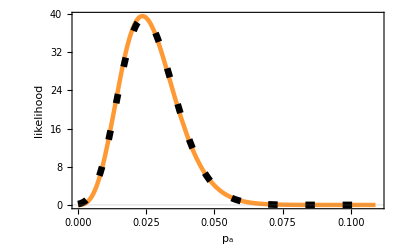

```mathematica
plot=Plot[{finalpost2[p]},{p,10.^-6,maxp},PlotRange->{{0,.11},All},PlotStyle->{{Thickness[.008],Lighter[Orange,.2]},{Dashing[{.017,.05}],Black,Thickness[.012]}},Frame->True,FrameStyle->16,FrameLabel->{"p_a","likelihood"},GridLines->{None,{0}}]
```

### BetaDistribution Code

```mathematica
(* NEW *)
Clear[root,α,β]
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
Clear[ptabstatesRound1,ntot,nyes]
AbsoluteTiming[Monitor[ptabstatesRound1=
Table[
length=Length[datastates[[i]]];

popstate=Total[datastates[[i,All,-1]]];
fracpop=datastates[[i,All,-1]]/popstate;

meanvartab=Table[newmeanvari3[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,length}];
meantab=meanvartab[[All,1]];
vartab=meanvartab[[All,2]];
μjoint=meantab.fracpop;
varjoint= vartab.fracpop^2;

{minp,maxp,dp}={Max[-p0,μjoint-5 √varjoint],Min[1,μjoint+8 √varjoint],3*(11 √varjoint)/(56*3)};
{minp,maxp,dp}={Rationalize[minp,10^-6],Rationalize[maxp+dp,10^-6],Rationalize[dp,10^-7]};

{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint-p0,V->varjoint};

root=FindRoot[μvarfun[α,β]=={μjoint,varjoint},{α,bestα,bestα/5,5bestα},{β,bestβ,bestβ/5,5bestβ},WorkingPrecision->32];
{bestα,bestβ}=Rationalize[{α/.root,β/.root},10^-9];

norm3=1/NIntegrate[beta[p-p0,bestα,bestβ],{p,0,5/10},WorkingPrecision->37];
finalpostbeta[p_]:=norm3 beta[p,bestα,bestβ];

ntot=Total[datastates[[i,All,3]]];nyes=Total[datastates[[i,All,4]]];

If[i==7,post[p_]:=(ntot+1)Binomial[ntot,nyes] Exp[nyes Log[p]+(ntot-nyes) Log[1-p]];
jacob=(1-FNR-FPR);postcorr[ptrue_]:=jacob post[pobs[ptrue]];
norm2=NIntegrate[postcorr[p],{p,0,1},WorkingPrecision->34];
finalpostbeta[p_]=postcorr[p+p0]/norm2;
];
result=p2σstatesfun[finalpostbeta,bestα/(bestα+bestβ),minp,maxp];
Join[result,Round[{bestα,bestβ},N[{bestα,bestβ},9]],{Round[√varjoint,10.^-7]}]
,{i,1,Length[datastates]}];
,{i,ntot,nyes,1. bestα/(bestα+bestβ),popstate}]]
ParallelEvaluate[On[NIntegrate::ncvb]];
MinMax[ptabstatesRound1[[All,5]]]
```

{0.0385,0.0165,0.0691,0.95}

FindRoot::reged: The point {0.0119331742243436754176610979} is at the edge of the search region {0.0119331742243436754176610979,0.0172122888200904304053717969} in coordinate 1 and the computed search direction points outside the region.

{0.0053,0.,0.0243,0.95}

{0.1135,0.0757,0.1592,0.95}

{0.0855,0.0511,0.1291,0.95}

{0.0088,0.0016,0.0182,0.95}

{0.0667,0.038,0.1037,0.95}

FindRoot::reged: The point {2.348937897978787668723199873241,253.81837470305093508763042225413} is at the edge of the search region {2.348937897978787668723199873241,58.723447449469691718079996831024} in coordinate 1 and the computed search direction points outside the region.

{0.,0.,0.0146,0.95}

FindRoot::reged: The point {0.0119331742243436754176610979} is at the edge of the search region {0.0119331742243436754176610979,0.0225680723282711341473050392} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

{0.0106,0.,0.0283,0.95}

{0.003,0.,0.0121,0.95}

{0.0111,0.,0.0361,0.95}

{0.0095,0.0023,0.0188,0.95}

{0.,0.,0.0235,0.95}

{0.0432,0.0012,0.1286,0.95}

{0.12,0.0908,0.1533,0.95}

{0.0151,0.0005,0.0379,0.95}

{0.0241,0.0076,0.0477,0.95}

{0.0302,0.004,0.0747,0.95}

{0.0053,0.0002,0.0116,0.95}

{0.0156,0.0011,0.038,0.95}

{0.0196,0.0036,0.0437,0.95}

{0.0005,0.,0.0218,0.95}

{0.0342,0.0119,0.0665,0.95}

{0.0043,0.0001,0.0093,0.95}

{0.005,0.0009,0.0099,0.95}

{0.,0.,0.0157,0.95}

{0.0199,0.0041,0.0432,0.95}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 27. digits of working precision to meet these tolerances.

{0.0035,0.,0.0105,0.95}

{349.044,Null}

{0.949996159124456739742998593,0.949999999767699343617842475}

{0.0385,0.0165,0.0691,0.95}

### Whole country

{19.4497,Null}

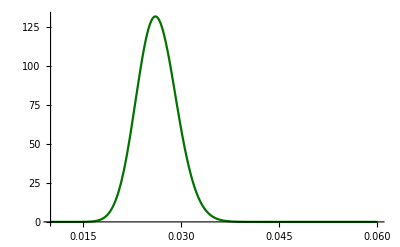

```mathematica
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
datacities=datacitiesr1;
ageQ[x_]:=x≤116;
totyesbins=Table[
casesyes=Select[datacities[[city,3,All,2]],ageQ[#]&];
casesno=Select[datacities[[city,4,All,2]],ageQ[#]&];
{Length[casesno]+Length[casesyes],Length[casesyes]}
,{city,1,Length[datacities]}];
datacities[[All,{3,4}]]=totyesbins;

AbsoluteTiming[
popstate=Total[datacities[[All,-1]]];
fracpop=datacities[[All,-1]]/popstate;
naivep=fracpop.(datacities[[All,4]]/(datacities[[All,3]]+1)); (* +1 to avoid error due to cities with 0 tests *)
{minp,maxp}=Rationalize[{Max[0,naivep-7/100],Min[1,naivep+8/100]},10^-4];

meanvartab=Table[newmeanvarihiprec[datacities[[k,4]],datacities[[k,3]]],{k,1,Length[datacities]}];
meantab=meanvartab[[All,1]];
vartab=meanvartab[[All,2]];
μjoint=meantab.fracpop ; (* μ before displacement *)
varjoint= vartab.fracpop^2;

{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint-p0,V->varjoint};

root=FindRoot[μvarfun[α,β]=={μjoint,varjoint},{α,bestα,bestα/5,5bestα},{β,bestβ,bestβ/5,5bestβ},WorkingPrecision->32];
{bestα,bestβ}=Rationalize[{α/.root,β/.root},10^-10];

norm=1/NIntegrate[beta[p-p0,bestα,bestβ],{p,0,5/10},WorkingPrecision->33];
finalpostbeta[p_]:=norm beta[p,bestα,bestβ];
]
ParallelEvaluate[On[NIntegrate::ncvb]];
pBrazilround1=Plot[finalpostbeta[p-p0],{p,.01,.06},PlotRange->All,PlotStyle->Darker[Green,.55]]
```

```mathematica
ParallelEvaluate[Off[NIntegrate::ncvb]];
ptabBrazilRound1=p2σstatesfun[finalpostbeta,bestα/(bestα+bestβ),μjoint-4 √varjoint-p0,μjoint+4 √varjoint-p0]
ParallelEvaluate[On[NIntegrate::ncvb]];
pBrazil1=Round[Join[ptabBrazilRound1,{bestα,bestβ,√varjoint}],.0001]
errorbrazilRound1=errorfun[{ptabBrazilRound1[[1;;4]]}][[1]]
```

{0.026,0.0204,0.0323,0.95}

{0.026037021329641095312647337,0.02619151704383080484567201852914,0.020397643616143418231988259,0.032269890669901419294792458,0.949999993940572500770208362}

{0.026,0.0262,0.0204,0.0323,0.95,152.412,3837.24,0.003}

Around[2.6037021329641095312647337,{0.5639377713497677080659078,0.623286934026032398214512}]

```mathematica
Round[{1.μjoint,√varjoint,1.μjoint-1.95 √varjoint,1.μjoint+1.98 √varjoint},.0001]
```

{0.0263,0.003,0.0204,0.0323}

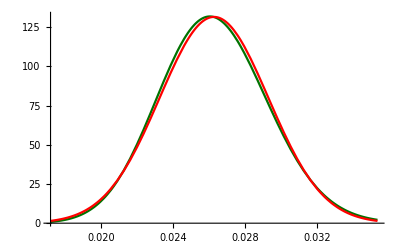

```mathematica
Plot[{finalpostbeta[p-p0],PDF[NormalDistribution[μjoint,√varjoint],p]},{p,μjoint-3 √varjoint+0p0,μjoint+3 √varjoint+0p0},PlotRange->All,PlotStyle->{Darker[Green,.55],Red}]
```

### Whole country - age bins

```mathematica
Clear[bin]
Monitor[
fatabr1=Table[
Switch[bin,1,ageQ[x_]:=x≤116,2,ageQ[x_]:=x≤29,3,ageQ[x_]:=30≤x≤49,4,ageQ[x_]:=50≤x≤69,5,ageQ[x_]:=x≥70];
datacities=datacitiesr1;
totyesbins=Table[
casesyes=Select[datacities[[city,3,All,2]],ageQ[#]&];
casesno=Select[datacities[[city,4,All,2]],ageQ[#]&];
{Length[casesno]+Length[casesyes],Length[casesyes]}
,{city,1,Length[datacities]}];
datacities[[All,{3,4}]]=totyesbins;

Off[FindMinimum::reged];
ParallelEvaluate[Off[NIntegrate::ncvb]];
popstate=Total[datacities[[All,-1]]];
fracpop=datacities[[All,-1]]/popstate;

meanvartab=Table[newmeanvari3[datacities[[k,4]],datacities[[k,3]]],{k,1,Length[datacities]}];
meantab=meanvartab[[All,1]];vartab=meanvartab[[All,2]];
μjoint=meantab.fracpop ; (* μ before displacement *)
varjoint= vartab.fracpop^2;
{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint-p0,V->varjoint};

root=FindRoot[μvarfun[α,β]=={μjoint,varjoint},{α,bestα,bestα/5,5bestα},{β,bestβ,bestβ/5,5bestβ},WorkingPrecision->32];
{bestα,bestβ}=Rationalize[{α/.root,β/.root},10^-10];

norm=1/NIntegrate[beta[p-p0,bestα,bestβ],{p,0,5/10},WorkingPrecision->33];
finalpostbeta[p_]:=norm beta[p,bestα,bestβ];

ParallelEvaluate[On[NIntegrate::ncvb]];
Round[{1.μjoint,√varjoint},.000001]
,{bin,1,5}],bin]
```

{{0.026269,0.003034},{0.039596,0.005908},{0.046608,0.006566},{0.050884,0.00647},{0.08599,0.01236}}

```mathematica
ptabBrazilRound1=p2σstatesfun[finalpostbeta,bestα/(bestα+bestβ),μjoint-4 √varjoint,μjoint+4 √varjoint]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0722039436859597021223299233}. NIntegrate obtained 4.74975137575796673014868507×10^-12 and 7.77070766582241575846659051×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0771472820481103035220948297}. NIntegrate obtained 3.57187150169158851937787024×10^-11 and 3.20759002091115424095043183×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0779896860215694012435123234}. NIntegrate obtained 3.25422160575892907521167732×10^-11 and 4.22285043454143095549184066×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.063462480912537674729429222}. NIntegrate obtained 3.11199456023126348687582121×10^-12 and 1.11524756829179049070270145×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0674654741798161363553191841}. NIntegrate obtained 1.67789448235134117830982738×10^-12 and 1.83494614220743935727711366×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0710230586247070631480244456}. NIntegrate obtained 6.36375656565848240136949839×10^-11 and 1.53141080305088773336471445×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0736506736315651415476737719}. NIntegrate obtained 2.24592921940657565857777998×10^-11 and 1.31733575198017126308449054×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0740740997611235609114220229}. NIntegrate obtained 6.66934724397844557913600549×10^-11 and 5.98916608119647251082265457×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0744752047611568241577456714}. NIntegrate obtained 4.03874008707666492709340873×10^-12 and 2.48614710962346099756544598×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0752217704705787645564667653}. NIntegrate obtained 3.07054877583731514076211353×10^-12 and 5.02349176316746715483117336×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0755716430694584881905938942}. NIntegrate obtained 1.64647087662452299016424511×10^-11 and 5.90046868110168328298089484×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0759082430795499202228354934}. NIntegrate obtained 4.43203405738665149409541359×10^-12 and 1.24875839549895712319854727×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.076232981920328077486817129}. NIntegrate obtained 7.22608685086964606040075169×10^-12 and 9.5657819421860537116643545×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.076547064995772235992242137}. NIntegrate obtained 5.06670945560350502949045911×10^-12 and 2.97184677776380343562744337×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0768515309694462697155001021}. NIntegrate obtained 4.07390492836629191759077882×10^-11 and 1.91373756437189487750152654×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.118542245890653324426767635}. NIntegrate obtained 9.31974859365310685376109754×10^-11 and 3.33992452866566477023906557×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0774351077200299930697097657}. NIntegrate obtained 2.30618412129499556205663214×10^-11 and 2.52204396706389541389831328×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0777157035121131168183811151}. NIntegrate obtained 7.15802349241295351050676685×10^-12 and 5.20711430002867344724499168×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.117460558492458928773640265}. NIntegrate obtained 6.36404423668563820470030239×10^-11 and 1.04117296697833237621939001×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.131981567788205766728991834}. NIntegrate obtained 8.12288748605937793221196651×10^-14 and 2.2886836637658424808476399×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0695415509430243345373181466}. NIntegrate obtained 3.13114892653157706559870861×10^-11 and 4.06314479527273865354442695×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.126815476296757787978655302}. NIntegrate obtained 8.13188024249034462273176384×10^-12 and 4.76970355270759463219849626×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.12516156367732565950583417}. NIntegrate obtained 2.67773997743864411123900426×10^-11 and 1.94792572769607371215704891×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0732012210486212625696153896}. NIntegrate obtained 6.53902589792676408956170355×10^-11 and 2.34339507659636093734329779×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.123174589703713988060981365}. NIntegrate obtained 7.86070194158148172755818882×10^-11 and 5.71827872324065054585609024×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.122601025198751485829564215}. NIntegrate obtained 1.0559911323334698461760767×10^-11 and 2.22478812126913285031374149×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.122060968225005526995508728}. NIntegrate obtained 4.68289273523690007334088516×10^-12 and 7.66132532008135079567133416×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0748569562527580564650992749}. NIntegrate obtained 3.92971135815285593706665111×10^-13 and 2.41903175852682994700542163×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.121064145741962938406158807}. NIntegrate obtained 9.08404882004931403171058012×10^-13 and 1.20253232440729679377462211×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.120600695572445277780209452}. NIntegrate obtained 3.79422915728862134251650744×10^-11 and 4.14937067062340290663152623×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.120157032228670811077304574}. NIntegrate obtained 8.94011877382993030781953969×10^-11 and 4.1996662711367032174398234×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.119731036585473196526035913}. NIntegrate obtained 3.48890650065757456363915124×10^-11 and 3.81546967972664271081658074×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.119320904942672902672852093}. NIntegrate obtained 1.12622812362972354782992126×10^-11 and 2.71021982416126210077951186×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.118925088370043988624516186}. NIntegrate obtained 2.02076137448293652067194735×10^-10 and 1.20992354525738212924728111×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.118171208016579697662540713}. NIntegrate obtained 3.29558929075884368852678747×10^-11 and 2.3973810840485389334459506×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.117810947931767851354925399}. NIntegrate obtained 2.15082313913040839605305668×10^-11 and 1.93146893330036546013647131×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.128932595340555107098918887}. NIntegrate obtained 2.49671049915448099206642464×10^-12 and 6.00822706154661954993570936×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.123787330289892677110768328}. NIntegrate obtained 6.09607387901332400280798874×10^-13 and 3.75259019597680658986701444×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.121549897441025509682772546}. NIntegrate obtained 4.46286506733472379772884151×10^-11 and 1.59935993541860715444584601×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0659313821793151623720610344}. NIntegrate obtained 1.69410186347230305442992651×10^-13 and 4.77325737459198537282042492×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0727210253294444873099724886}. NIntegrate obtained 1.22644874586550253065434343×10^-11 and 2.58391241847904354476144719×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0686119053306646914143479755}. NIntegrate obtained 1.04438147379494947409551785×10^-11 and 6.12575428313832374023669603×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.070331391102615086066142631}. NIntegrate obtained 7.78322032763536705963001144×10^-11 and 2.78927785774858342966418404×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0716417519808697902598123151}. NIntegrate obtained 3.63915127303369504035008978×10^-11 and 3.97977742452322771534932679×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.134298991007497636815281974}. NIntegrate obtained 1.63154618360832500344916071×10^-13 and 6.33197692587570509810710711×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0804639641425118975556595902}. NIntegrate obtained 1.66495014431872691140473611×10^-11 and 4.69112024825788775356872267×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0782576050511918079573681388}. NIntegrate obtained 9.49230343446224599539904669×10^-12 and 1.03807872028683008130170574×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0787771757856493447125479988}. NIntegrate obtained 8.43045022726447604655042832×10^-12 and 9.21954406948282082693700963×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0792778144099094569165770938}. NIntegrate obtained 5.4247567916570324252970144×10^-11 and 1.94407371564663081944481582×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0795219313928259606080092975}. NIntegrate obtained 4.62342118631199393120800225×10^-11 and 2.71183881217792786894108356×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.079999299542289419066403815}. NIntegrate obtained 1.36342082987135081838244144×10^-10 and 6.4047387045860446892715775×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0811412042150827367446718979}. NIntegrate obtained 6.18969009344000626984852346×10^-12 and 1.30405915109878800688804251×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0785199535569758469984412659}. NIntegrate obtained 1.5253082396964926221577718×10^-12 and 3.21355696040578799360260735×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0790296740524809637705081959}. NIntegrate obtained 1.12577805952703574418928744×10^-11 and 2.37181693816942652311324566×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.081581871879590036750225967}. NIntegrate obtained 9.16350547283084592939130076×10^-11 and 5.3747968859478946836875567×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0797623320853577154789938386}. NIntegrate obtained 6.71746116788288807884519971×10^-11 and 1.41525126021519634357668185×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0802330957292973350818367074}. NIntegrate obtained 5.36094650325936708174778×10^-12 and 1.51048635170060750059225973×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.114356617822780996752164447}. NIntegrate obtained 7.27441160604458126648344944×10^-12 and 7.95529972605513350041298011×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0806921319409940902890058322}. NIntegrate obtained 7.16927261651392988859714195×10^-11 and 6.43810598767555296681264228×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.117119233576778735624828606}. NIntegrate obtained 1.40348450568634536985126428×10^-10 and 5.0296767969090409476562572×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0809178119170170809800411179}. NIntegrate obtained 3.66614147600598113111841427×10^-11 and 2.15035237890860607544831793×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0813624978239954865356654058}. NIntegrate obtained 1.28518811560796538349757092×10^-10 and 1.40548228675362692606823777×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.116460970626019709849060214}. NIntegrate obtained 1.63951913889737567500905044×10^-11 and 2.17037006285078143779591414×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.115831221122465678490323182}. NIntegrate obtained 5.07264141705475182188509911×10^-13 and 3.12259083915718376737291196×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.112988848101488133555979012}. NIntegrate obtained 6.40533193683387412680052869×10^-12 and 2.2954830862817722565033172×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.11552574461996212580525784}. NIntegrate obtained 4.62460794950477840582589348×10^-11 and 3.36417758443275291150325215×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.115225933748912666905517505}. NIntegrate obtained 2.80205180074526884118116221×10^-11 and 3.70931280909382836041356559×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.114931385245503008669151517}. NIntegrate obtained 5.25814031423239836951651013×10^-11 and 2.47003816168096916679206845×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.114641727718739649980336121}. NIntegrate obtained 1.23067760557225382640690964×10^-10 and 1.59699248845428543801075192×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.114075736971276575411639685}. NIntegrate obtained 7.27121984145610307243435699×10^-12 and 5.2894591442112579822774359×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.11379878847708215831098246}. NIntegrate obtained 2.57419540824129493746707706×10^-11 and 1.50987823479056109933197279×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.11352549503916308501416569}. NIntegrate obtained 1.44321559099565821287882839×10^-12 and 4.0663667348319201162950878×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.116786253161520270110998848}. NIntegrate obtained 2.19766643512444240118780536×10^-10 and 2.40336897528283060872011402×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.113255596542018169082331092}. NIntegrate obtained 3.00981422588866440551851001×10^-11 and 2.18949360979764670140724359×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.116142802795218748552311215}. NIntegrate obtained 6.79950836013041452913884526×10^-11 and 4.9463119591805611486793549×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0817994969346189914691523398}. NIntegrate obtained 9.67184956626193100522120397×10^-11 and 2.03768908302627295948006311×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0820155359799668909059304668}. NIntegrate obtained 1.71289663292295280443728146×10^-11 and 8.0464190725389646339554743×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0822301454757150604909763461}. NIntegrate obtained 2.4139385741278267713621054×10^-11 and 2.63988428431020346858573648×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.112725018338293234555220285}. NIntegrate obtained 5.72271211961930871827326521×10^-11 and 5.13907465090754475088461257×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.112463887802917596853159372}. NIntegrate obtained 1.00340652428384114713617067×10^-11 and 2.11400157440311197605193939×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.112205247600046911169125298}. NIntegrate obtained 1.1392338469685260454332209×10^-11 and 1.02304775478912198374572104×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0826556741833067797328446159}. NIntegrate obtained 2.22417886571384283265279476×10^-10 and 5.35239133532098843247579686×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0824434762197101276595408499}. NIntegrate obtained 1.38410540824450650388383619×10^-10 and 8.11838379901728319610640153×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.111694647820140313474599963}. NIntegrate obtained 1.5631466172995605055544967×10^-10 and 7.34296075330025276001394704×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.111948898111838670486460793}. NIntegrate obtained 2.19112278225524466813575017×10^-11 and 2.90057442938590459404571506×10^-12 for the integral and error estimates.

{0.0846,0.0623,0.1105,0.95}

{0.084592220608188091668639401,0.08552590668703279226858935176608,0.062261869650554266407916656,0.11050467527723611297725948,0.949999993528160318990189812}

```mathematica
Round[fatabr1,.0001]
```

{{0.0263,0.003},{0.0396,0.0059},{0.0466,0.0066},{0.0509,0.0065},{0.086,0.0124}}

## Main Calculations - 2nd round

```mathematica
datacities=datacities3rounds[[All,{1,2,4,7,-1}]];
```

### Combining states

```mathematica
datacities=datacities3rounds[[All,{1,2,4,7,-1}]];
datacities[[All,1]]
statesindex={1,3,5,9,11,21,27,28,32,38,43,56,59,64,71,75,79,85,91,96,99,101,103,111,118,120,131,134};
datastates=Table[datacities[[statesindex[[i]];;(statesindex[[i+1]]-1)]],{i,Length[statesindex]-1}];
statesnames=datastates[[All,1,1]];
Dimensions[datastates]
datastates[[All,1,1]]
datastates[[1;;5]]
ncities=Table[Length[datastates[[i]]],{i,Length[datastates]}]
ilist=Flatten[Position[ncities,n_ /; n<5],1]
```

{AC,AC,AL,AL,AM,AM,AM,AM,AP,AP,BA,BA,BA,BA,BA,BA,BA,BA,BA,BA,CE,CE,CE,CE,CE,CE,DF,ES,ES,ES,ES,GO,GO,GO,GO,GO,GO,MA,MA,MA,MA,MA,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MS,MS,MS,MT,MT,MT,MT,MT,PA,PA,PA,PA,PA,PA,PA,PB,PB,PB,PB,PE,PE,PE,PE,PI,PI,PI,PI,PI,PI,PR,PR,PR,PR,PR,PR,RJ,RJ,RJ,RJ,RJ,RN,RN,RN,RO,RO,RR,RR,RS,RS,RS,RS,RS,RS,RS,RS,SC,SC,SC,SC,SC,SC,SC,SE,SE,SP,SP,SP,SP,SP,SP,SP,SP,SP,SP,SP,TO,TO,TO}

{27}

{AC,AL,AM,AP,BA,CE,DF,ES,GO,MA,MG,MS,MT,PA,PB,PE,PI,PR,RJ,RN,RO,RR,RS,SC,SE,SP,TO}

{{{AC,CRUZEIRO DO SUL,250,33,88376},{AC,RIO BRANCO,250,10,407319}},{{AL,ARAPIRACA,250,6,231747},{AL,MACEIÓ,250,26,1018948}},{{AM,LÁBREA,250,8,46069},{AM,MANAUS,250,31,2182763},{AM,PARINTINS,250,24,114273},{AM,TEFÉ,250,43,59849}},{{AP,MACAPÁ,250,32,503327},{AP,OIAPOQUE,250,11,27270}},{{BA,BARREIRAS,250,0,155439},{BA,FEIRA DE SANTANA,208,1,614872},{BA,GUANAMBI,250,0,84481},{BA,IRECÊ,250,0,72967},{BA,ITABUNA,200,1,213223},{BA,JUAZEIRO,250,0,216707},{BA,PAULO AFONSO,250,1,117782},{BA,SALVADOR,215,10,2872347},{BA,SANTO ANTÔNIO DE JESUS,0,0,101512},{BA,VITÓRIA DA CONQUISTA,250,0,338480}}}

{2,2,4,2,10,6,1,4,6,5,13,3,5,7,4,4,6,6,5,3,2,2,8,7,2,11,3}

{1,2,3,4,7,8,12,15,16,20,21,22,25,27}

```mathematica
Total[datastates[[All,All,3]],{2}]
totround2=Total[%]
```

{500,500,1000,500,2123,1402,250,1000,1500,1232,3163,703,1112,1750,1000,942,1500,1094,1145,603,500,500,1881,1594,500,2471,700}

31165

```mathematica
datastates//TableForm
```

AC
CRUZEIRO DO SUL
250
33
88376 | AC
RIO BRANCO
250
10
407319 |  |  |  |  |  |  |  |  |  |  | 
AL
ARAPIRACA
250
6
231747 | AL
MACEIÓ
250
26
1018948 |  |  |  |  |  |  |  |  |  |  | 
AM
LÁBREA
250
8
46069 | AM
MANAUS
250
31
2182763 | AM
PARINTINS
250
24
114273 | AM
TEFÉ
250
43
59849 |  |  |  |  |  |  |  |  | 
AP
MACAPÁ
250
32
503327 | AP
OIAPOQUE
250
11
27270 |  |  |  |  |  |  |  |  |  |  | 
BA
BARREIRAS
250
0
155439 | BA
FEIRA DE SANTANA
208
1
614872 | BA
GUANAMBI
250
0
84481 | BA
IRECÊ
250
0
72967 | BA
ITABUNA
200
1
213223 | BA
JUAZEIRO
250
0
216707 | BA
PAULO AFONSO
250
1
117782 | BA
SALVADOR
215
10
2872347 | BA
SANTO ANTÔNIO DE JESUS
0
0
101512 | BA
VITÓRIA DA CONQUISTA
250
0
338480 |  |  | 
CE
CRATEÚS
250
2
75074 | CE
FORTALEZA
226
30
2669342 | CE
IGUATU
250
2
102498 | CE
JUAZEIRO DO NORTE
250
3
274207 | CE
QUIXADÁ
250
3
87728 | CE
SOBRAL
176
33
208935 |  |  |  |  |  |  | 
DF
BRASÍLIA
250
2
3015268 |  |  |  |  |  |  |  |  |  |  |  | 
ES
CACHOEIRO DE ITAPEMIRIM
250
3
208972 | ES
COLATINA
250
2
122499 | ES
SÃO MATEUS
250
0
130611 | ES
VITÓRIA
250
7
362097 |  |  |  |  |  |  |  |  | 
GO
GOIÂNIA
250
0
1516113 | GO
IPORÁ
250
0
31531 | GO
ITUMBIARA
250
0
104742 | GO
LUZIÂNIA
250
3
208299 | GO
PORANGATU
250
0
45394 | GO
RIO VERDE
250
1
235647 |  |  |  |  |  |  | 
MA
BACABAL
250
10
104949 | MA
CAXIAS
250
1
164880 | MA
IMPERATRIZ
250
35
258682 | MA
PRESIDENTE DUTRA
250
18
47804 | MA
SÃO LUÍS
232
13
1101884 |  |  |  |  |  |  |  | 
MG
BARBACENA
250
0
137313 | MG
BELO HORIZONTE
250
0
2512070 | MG
DIVINÓPOLIS
250
0
238230 | MG
GOVERNADOR VALADARES
189
1
279885 | MG
IPATINGA
224
0
263410 | MG
JUIZ DE FORA
250
0
568873 | MG
MONTES CLAROS
250
0
409341 | MG
PATOS DE MINAS
250
0
152488 | MG
POUSO ALEGRE
250
0
150737 | MG
TEÓFILO OTONI
250
2
140592 | MG
UBERABA
250
0
333783 | MG
UBERLÂNDIA
250
0
691305 | MG
VARGINHA
250
0
135558
MS
CAMPO GRANDE
203
0
895982 | MS
CORUMBÁ
250
0
111435 | MS
DOURADOS
250
1
222949 |  |  |  |  |  |  |  |  |  | 
MT
BARRA DO GARÇAS
250
1
61012 | MT
CÁCERES
215
0
94376 | MT
CUIABÁ
250
3
612547 | MT
RONDONÓPOLIS
147
2
232491 | MT
SINOP
250
0
142996 |  |  |  |  |  |  |  | 
PA
ALTAMIRA
250
6
114594 | PA
BELÉM
250
36
1492745 | PA
BREVES
250
26
102701 | PA
CASTANHAL
250
23
200793 | PA
MARABÁ
250
22
279349 | PA
REDENÇÃO
250
3
84787 | PA
SANTARÉM
250
23
304589 |  |  |  |  |  | 
PB
CAMPINA GRANDE
250
14
409731 | PB
JOÃO PESSOA
250
13
809015 | PB
PATOS
250
3
107605 | PB
SOUSA
250
2
69444 |  |  |  |  |  |  |  |  | 
PE
CARUARU
222
4
361118 | PE
PETROLINA
250
0
349145 | PE
RECIFE
220
6
1645727 | PE
SERRA TALHADA
250
2
86350 |  |  |  |  |  |  |  |  | 
PI
CORRENTE
250
0
26644 | PI
FLORIANO
250
0
59935 | PI
PARNAÍBA
250
12
153078 | PI
PICOS
250
1
78222 | PI
SÃO RAIMUNDO NONATO
250
0
34710 | PI
TERESINA
250
3
864845 |  |  |  |  |  |  | 
PR
CASCAVEL
250
0
328454 | PR
CURITIBA
123
0
1933105 | PR
GUARAPUAVA
250
0
181504 | PR
LONDRINA
111
0
569733 | PR
MARINGÁ
126
0
423666 | PR
PONTA GROSSA
234
0
351736 |  |  |  |  |  |  | 
RJ
CAMPOS DOS GOYTACAZES
189
2
507548 | RJ
MACAÉ
206
1
256672 | RJ
PETRÓPOLIS
250
1
306191 | RJ
RIO DE JANEIRO
250
16
6718903 | RJ
VOLTA REDONDA
250
1
273012 |  |  |  |  |  |  |  | 
RN
CAICÓ
250
0
67952 | RN
MOSSORÓ
112
6
297378 | RN
NATAL
241
7
884122 |  |  |  |  |  |  |  |  |  | 
RO
JI-PARANÁ
250
2
128969 | RO
PORTO VELHO
250
7
529544 |  |  |  |  |  |  |  |  |  |  | 
RR
BOA VISTA
250
54
399213 | RR
RORAINÓPOLIS
250
22
30163 |  |  |  |  |  |  |  |  |  |  | 
RS
CAXIAS DO SUL
250
0
510906 | RS
IJUÍ
176
1
83475 | RS
PASSO FUNDO
233
1
203275 | RS
PELOTAS
250
0
342405 | RS
PORTO ALEGRE
230
0
1483771 | RS
SANTA CRUZ DO SUL
250
0
130416 | RS
SANTA MARIA
242
0
282123 | RS
URUGUAIANA
250
0
126970 |  |  |  |  | 
SC
BLUMENAU
239
1
357199 | SC
CAÇADOR
250
0
78595 | SC
CHAPECÓ
250
0
220367 | SC
CRICIÚMA
185
0
215186 | SC
FLORIANÓPOLIS
205
0
500973 | SC
JOINVILLE
250
0
590466 | SC
LAGES
215
0
157544 |  |  |  |  |  | 
SE
ARACAJU
250
2
657013 | SE
ITABAIANA
250
3
95427 |  |  |  |  |  |  |  |  |  |  | 
SP
ARAÇATUBA
250
1
197016 | SP
ARARAQUARA
247
0
236072 | SP
BAURU
250
1
376818 | SP
CAMPINAS
250
1
1204073 | SP
MARÍLIA
250
0
238882 | SP
PRESIDENTE PRUDENTE
250
0
228743 | SP
RIBEIRÃO PRETO
250
0
703293 | SP
SÃO JOSÉ DO RIO PRETO
94
0
460671 | SP
SÃO JOSÉ DOS CAMPOS
170
0
721944 | SP
SÃO PAULO
250
5
12252023 | SP
SOROCABA
210
1
679378 |  | 
TO
ARAGUAÍNA
200
2
180470 | TO
GURUPI
250
0
86647 | TO
PALMAS
250
1
299127 |  |  |  |  |  |  |  |  |  |

### Exact Code

```mathematica
ilist=Flatten[Position[ncities,n_ /; n<5],1]
```

{1,2,3,4,7,8,12,15,16,20,21,22,25,27}

```mathematica
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
ParallelEvaluate[Off[NIntegrate::slwcon]];
Clear[ntot,nyes,finalpost,jointpost,pvec]
AbsoluteTiming[Monitor[ptabstatesRound2exact=
Table[
tab=Table[
ntot=datastates[[i,j,3]];
nyes=datastates[[i,j,4]];
post[p_]:=(ntot+1)Binomial[ntot,nyes] Exp[nyes Log[p]+(ntot-nyes) Log[1-p]];
(*norm=NIntegrate[posttest[p],{p,0,1},AccuracyGoal->9,WorkingPrecision->28];
post[p_]=post[p]/norm;*)
jacob=(1-FNR-FPR);
postcorr[ptrue_]:=jacob post[pobs[ptrue]];
(*NIntegrate[postcorr[p],{p,p0,ptrue[1]}];*)
norm2=NIntegrate[postcorr[p],{p,0,1},AccuracyGoal->9+1,WorkingPrecision->30+20]; (* Must be one *)
postcorr[p_]=postcorr[p]/norm2
,{j,1,Length[datastates[[i]]]}];

popstate=Total[datastates[[i,All,5]]];
fracpop=datastates[[i,All,5]]/popstate;
ntot=Total[datastates[[i,All,3]]];nyes=Total[datastates[[i,All,4]]];

vartab=Table[vari[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,Length[tab]}];
varjoint=vartab.fracpop^2;
meantab=Table[meani[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,Length[tab]}];
μjoint=meantab.fracpop;
{minp,maxp,dp}={Max[1/1000000,μjoint-6 √varjoint],Min[1,μjoint+7 √varjoint],(11 √varjoint)/105};
{minp,maxp,dp}={Rationalize[minp,10^-6],Rationalize[maxp+dp,10^-6],Rationalize[dp,10^-7]};

pvec=pname[[1;;Length[tab]]];
jointpost[pvec_]=Module[{aux=1},
Do[aux*=(tab[[j]]/.p->pname[[j]]);,{j,Length[tab]}];
aux];
delta[pvec_]:=Sum[pname[[j]] fracpop[[j]],{j,Length[pvec]}];
norma[pvec_]:=Norm[Table[D[delta[pvec], pname[[j]]],{j,Length[pvec]}]];
logicfun[pvec_]:=Apply[And,Flatten[Table[{GreaterEqual[pvec[[j]],0],LessEqual[pvec[[j]],1]},{j,Length[pvec]}]]];
reg[p_]=ImplicitRegion[p==delta[pvec]∧logicfun[pvec],Evaluate[pvec]];
If[i==19,finalpost[p_]:=NIntegrate[jointpost[pvec]/norma[pvec],pvec∈reg[p],AccuracyGoal->35,PrecisionGoal->4,WorkingPrecision->39];,
finalpost[p_]:=NIntegrate[jointpost[pvec]/norma[pvec],pvec∈reg[p],AccuracyGoal->6+0,PrecisionGoal->4+0,WorkingPrecision->26+2];];

finalposttab=ParallelMap[{#,finalpost[#]}&,Range[minp,maxp+dp,dp]];
finalpost2=Interpolation[finalposttab,InterpolationOrder->3];
ntot=Total[datastates[[i,All,3]]];
nyes=Total[datastates[[i,All,4]]];
NotebookSave[];
result=p2σstatesexactfun[finalpost2,μjoint(2/3),minp,maxp];
Prepend[result,i]
,{i,ilist}];
,{i,ntot,nyes,1.μjoint,popstate,result[[2]],1.minp,1.maxp}]]
ParallelEvaluate[On[NIntegrate::ncvb]];
ParallelEvaluate[On[NIntegrate::slwcon]];
```

3

{0.074,0.0765,0.0447,0.1128,0.95}

{588.276,Null}

1.×10^-6

```mathematica
Round[result,.000001]
```

{0.074004,0.076469,0.044733,0.112752,0.95}

### BetaDistribution Code

```mathematica
(* NEW *)
Clear[root,α,β]
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
Clear[ptabstatesRound2,ntot,nyes]
AbsoluteTiming[Monitor[ptabstatesRound2=
Table[
length=Length[datastates[[i]]];

popstate=Total[datastates[[i,All,-1]]];
fracpop=datastates[[i,All,-1]]/popstate;

meanvartab=Table[newmeanvari3[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,length}];
meantab=meanvartab[[All,1]];
vartab=meanvartab[[All,2]];
μjoint=meantab.fracpop;
varjoint= vartab.fracpop^2;

{minp,maxp,dp}={Max[-p0,μjoint-5 √varjoint],Min[1,μjoint+8 √varjoint],3*(11 √varjoint)/(56*3)};
{minp,maxp,dp}={Rationalize[minp,10^-6],Rationalize[maxp+dp,10^-6],Rationalize[dp,10^-7]};

{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint-p0,V->varjoint};

root=FindRoot[μvarfun[α,β]=={μjoint,varjoint},{α,bestα,bestα/5,5bestα},{β,bestβ,bestβ/5,5bestβ},WorkingPrecision->32];
{bestα,bestβ}=Rationalize[{α/.root,β/.root},10^-9];

norm3=1/NIntegrate[beta[p-p0,bestα,bestβ],{p,0,5/10},WorkingPrecision->37];
finalpostbeta[p_]:=norm3 beta[p,bestα,bestβ];

ntot=Total[datastates[[i,All,3]]];nyes=Total[datastates[[i,All,4]]];

If[i==7,post[p_]:=(ntot+1)Binomial[ntot,nyes] Exp[nyes Log[p]+(ntot-nyes) Log[1-p]];
jacob=(1-FNR-FPR);postcorr[ptrue_]:=jacob post[pobs[ptrue]];
norm2=NIntegrate[postcorr[p],{p,0,1},WorkingPrecision->34];
finalpostbeta[p_]=postcorr[p+p0]/norm2;
];
result=p2σstatesfun[finalpostbeta,bestα/(bestα+bestβ),minp,maxp];
Join[result,Round[{bestα,bestβ},N[{bestα,bestβ},9]],{Round[√varjoint,10.^-7]}]
,{i,1,Length[datastates]}];
,{i,ntot,nyes,1. bestα/(bestα+bestβ),popstate}]]
ParallelEvaluate[On[NIntegrate::ncvb]];
MinMax[ptabstatesRound2[[All,5]]]
```

{0.0491,0.0274,0.0769,0.95}

{0.131,0.0928,0.176,0.95}

{0.0745,0.0444,0.1127,0.95}

{0.1318,0.0897,0.182,0.95}

{0.0231,0.0091,0.042,0.95}

{0.1758,0.1347,0.2221,0.95}

{0.,0.,0.0216,0.95}

{0.0264,0.0133,0.0433,0.95}

{0.0095,0.0002,0.0226,0.95}

{0.0705,0.0489,0.0962,0.95}

{0.0063,0.001,0.0128,0.95}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 27. digits of working precision to meet these tolerances.

{0.0049,0.,0.0153,0.95}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 27. digits of working precision to meet these tolerances.

{0.0061,0.,0.0145,0.95}

{0.0628,0.0447,0.0842,0.95}

{0.0167,0.0045,0.0334,0.95}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 27. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{0.0064,0.,0.0197,0.95}

{0.0809,0.0539,0.1137,0.95}

{0.0079,0.0021,0.0151,0.95}

{0.0792,0.0482,0.1182,0.95}

{0.0488,0.0271,0.0767,0.95}

{0.0529,0.0277,0.0863,0.95}

{0.2049,0.1542,0.2621,0.95}

{0.0046,0.0004,0.0098,0.95}

{0.0059,0.0013,0.0114,0.95}

{0.0266,0.0075,0.0549,0.95}

FindRoot::reged: The point {0.0119331742243436754176610979} is at the edge of the search region {0.0119331742243436754176610979,0.0188812477376486438254304782} in coordinate 1 and the computed search direction points outside the region.

{0.0069,0.,0.0205,0.95}

{0.0121,0.0035,0.0234,0.95}

{388.389,Null}

{0.949967809257069599526724181,0.949999999987306577016555365}

### Whole country

{24.264,Null}

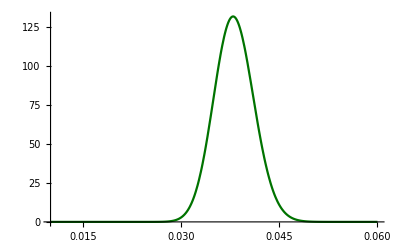

```mathematica
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
datacities=datacitiesr2;
ageQ[x_]:=x≤116;
totyesbins=Table[
casesyes=Select[datacities[[city,3,All,2]],ageQ[#]&];
casesno=Select[datacities[[city,4,All,2]],ageQ[#]&];
{Length[casesno]+Length[casesyes],Length[casesyes]}
,{city,1,Length[datacities]}];
datacities[[All,{3,4}]]=totyesbins;

AbsoluteTiming[
popstate=Total[datacities[[All,-1]]];
fracpop=datacities[[All,-1]]/popstate;
naivep=fracpop.(datacities[[All,4]]/(datacities[[All,3]]+1)); (* +1 to avoid error due to cities with 0 tests *)
{minp,maxp}=Rationalize[{Max[0,naivep-7/100],Min[1,naivep+8/100]},10^-4];

meanvartab=Table[newmeanvarihiprec[datacities[[k,4]],datacities[[k,3]]],{k,1,Length[datacities]}];
meantab=meanvartab[[All,1]];
vartab=meanvartab[[All,2]];
μjoint=meantab.fracpop ; (* μ before displacement *)
varjoint= vartab.fracpop^2;

{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint-p0,V->varjoint};

root=FindRoot[μvarfun[α,β]=={μjoint,varjoint},{α,bestα,bestα/5,5bestα},{β,bestβ,bestβ/5,5bestβ},WorkingPrecision->32];
{bestα,bestβ}=Rationalize[{α/.root,β/.root},10^-10];

norm=1/NIntegrate[beta[p-p0,bestα,bestβ],{p,0,3/10},WorkingPrecision->33];
finalpostbeta[p_]:=norm beta[p,bestα,bestβ];
]
ParallelEvaluate[On[NIntegrate::ncvb]];
pBrazilround2=Plot[finalpostbeta[p-p0],{p,.01,.06},PlotRange->All,PlotStyle->Darker[Green,.55]]
```

```mathematica
ParallelEvaluate[Off[NIntegrate::ncvb]];
ptabBrazilRound2=p2σstatesfun[finalpostbeta,bestα/(bestα+bestβ),μjoint-4 √varjoint-p0,μjoint+4 √varjoint-p0]
ParallelEvaluate[On[NIntegrate::ncvb]];
pBrazil2=Round[Join[ptabBrazilRound2,{bestα,bestβ,√varjoint}],.0001]
errorbrazilRound2=errorfun[{ptabBrazilRound2[[1;;4]]}][[1]]
```

{0.0379,0.0322,0.0441,0.95}

{0.037922027213898047618997363,0.03803856237437719935554234327018,0.032200960072005573492530138,0.044090563234679065400571552,0.949999993807873216877894581}

{0.0379,0.038,0.0322,0.0441,0.95,257.857,4896.21,0.003}

Around[3.7922027213898047618997363,{0.5721067141892474126467225,0.616853602078101778157419}]

### Whole country - age bins

```mathematica
Clear[bin]
Monitor[
fatabr2=Table[
Switch[bin,1,ageQ[x_]:=x≤116,2,ageQ[x_]:=x≤29,3,ageQ[x_]:=30≤x≤49,4,ageQ[x_]:=50≤x≤69,5,ageQ[x_]:=x≥70];
datacities=datacitiesr2;
totyesbins=Table[
casesyes=Select[datacities[[city,3,All,2]],ageQ[#]&];
casesno=Select[datacities[[city,4,All,2]],ageQ[#]&];
{Length[casesno]+Length[casesyes],Length[casesyes]}
,{city,1,Length[datacities]}];
datacities[[All,{3,4}]]=totyesbins;

Off[FindMinimum::reged];
ParallelEvaluate[Off[NIntegrate::ncvb]];
popstate=Total[datacities[[All,-1]]];
fracpop=datacities[[All,-1]]/popstate;

meanvartab=Table[newmeanvari3[datacities[[k,4]],datacities[[k,3]]],{k,1,Length[datacities]}];
meantab=meanvartab[[All,1]];vartab=meanvartab[[All,2]];
μjoint=meantab.fracpop ; (* μ before displacement *)
varjoint= vartab.fracpop^2;
{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint-p0,V->varjoint};

root=FindRoot[μvarfun[α,β]=={μjoint,varjoint},{α,bestα,bestα/5,5bestα},{β,bestβ,bestβ/5,5bestβ},WorkingPrecision->32];
{bestα,bestβ}=Rationalize[{α/.root,β/.root},10^-10];

norm=1/NIntegrate[beta[p-p0,bestα,bestβ],{p,0,3/10},WorkingPrecision->33];
finalpostbeta[p_]:=norm beta[p,bestα,bestβ];

ParallelEvaluate[On[NIntegrate::ncvb]];
Round[{1.μjoint,√varjoint},.000001]
,{bin,1,5}],bin]
Round[fatabr2,.0001]
```

{{0.038097,0.003036},{0.036849,0.004891},{0.060508,0.006153},{0.05527,0.006923},{0.092581,0.015636}}

{{0.0381,0.003},{0.0368,0.0049},{0.0605,0.0062},{0.0553,0.0069},{0.0926,0.0156}}

## Main Calculations - 3rd round

```mathematica
datacities=datacities3rounds[[All,{1,2,5,8,-1}]];
statesindex={1,3,5,9,11,21,27,28,32,38,43,56,59,64,71,75,79,85,91,96,99,101,103,111,118,120,131,134};
datastates=Table[datacities[[statesindex[[i]];;(statesindex[[i+1]]-1)]],{i,Length[statesindex]-1}];
statesnames=datastates[[All,1,1]];
```

### Combining states

```mathematica
datacities=datacities3rounds[[All,{1,2,5,8,-1}]];
datacities[[All,1]]
statesindex={1,3,5,9,11,21,27,28,32,38,43,56,59,64,71,75,79,85,91,96,99,101,103,111,118,120,131,134};
datastates=Table[datacities[[statesindex[[i]];;(statesindex[[i+1]]-1)]],{i,Length[statesindex]-1}];
statesnames=datastates[[All,1,1]];
Dimensions[datastates]
datastates[[All,1,1]]
datastates[[1;;5]]
ncities=Table[Length[datastates[[i]]],{i,Length[datastates]}]
ilist=Flatten[Position[ncities,n_ /; n<5],1]
```

{AC,AC,AL,AL,AM,AM,AM,AM,AP,AP,BA,BA,BA,BA,BA,BA,BA,BA,BA,BA,CE,CE,CE,CE,CE,CE,DF,ES,ES,ES,ES,GO,GO,GO,GO,GO,GO,MA,MA,MA,MA,MA,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MG,MS,MS,MS,MT,MT,MT,MT,MT,PA,PA,PA,PA,PA,PA,PA,PB,PB,PB,PB,PE,PE,PE,PE,PI,PI,PI,PI,PI,PI,PR,PR,PR,PR,PR,PR,RJ,RJ,RJ,RJ,RJ,RN,RN,RN,RO,RO,RR,RR,RS,RS,RS,RS,RS,RS,RS,RS,SC,SC,SC,SC,SC,SC,SC,SE,SE,SP,SP,SP,SP,SP,SP,SP,SP,SP,SP,SP,TO,TO,TO}

{27}

{AC,AL,AM,AP,BA,CE,DF,ES,GO,MA,MG,MS,MT,PA,PB,PE,PI,PR,RJ,RN,RO,RR,RS,SC,SE,SP,TO}

{{{AC,CRUZEIRO DO SUL,250,28,88376},{AC,RIO BRANCO,250,9,407319}},{{AL,ARAPIRACA,250,11,231747},{AL,MACEIÓ,250,34,1018948}},{{AM,LÁBREA,250,17,46069},{AM,MANAUS,250,17,2182763},{AM,PARINTINS,250,26,114273},{AM,TEFÉ,250,37,59849}},{{AP,MACAPÁ,250,31,503327},{AP,OIAPOQUE,250,12,27270}},{{BA,BARREIRAS,250,1,155439},{BA,FEIRA DE SANTANA,250,5,614872},{BA,GUANAMBI,250,0,84481},{BA,IRECÊ,250,0,72967},{BA,ITABUNA,250,8,213223},{BA,JUAZEIRO,250,10,216707},{BA,PAULO AFONSO,211,2,117782},{BA,SALVADOR,250,8,2872347},{BA,SANTO ANTÔNIO DE JESUS,250,3,101512},{BA,VITÓRIA DA CONQUISTA,250,0,338480}}}

{2,2,4,2,10,6,1,4,6,5,13,3,5,7,4,4,6,6,5,3,2,2,8,7,2,11,3}

{1,2,3,4,7,8,12,15,16,20,21,22,25,27}

```mathematica
Total[datastates[[All,All,3]],{2}]
totround3=Total[%]
```

{500,500,1000,500,2461,1500,250,1000,1500,1250,3250,750,1250,1750,1000,1000,1500,1500,1250,750,500,500,2000,1750,496,2750,750}

33207

```mathematica
datastates//TableForm
```

AC
CRUZEIRO DO SUL
250
28
88376 | AC
RIO BRANCO
250
9
407319 |  |  |  |  |  |  |  |  |  |  | 
AL
ARAPIRACA
250
11
231747 | AL
MACEIÓ
250
34
1018948 |  |  |  |  |  |  |  |  |  |  | 
AM
LÁBREA
250
17
46069 | AM
MANAUS
250
17
2182763 | AM
PARINTINS
250
26
114273 | AM
TEFÉ
250
37
59849 |  |  |  |  |  |  |  |  | 
AP
MACAPÁ
250
31
503327 | AP
OIAPOQUE
250
12
27270 |  |  |  |  |  |  |  |  |  |  | 
BA
BARREIRAS
250
1
155439 | BA
FEIRA DE SANTANA
250
5
614872 | BA
GUANAMBI
250
0
84481 | BA
IRECÊ
250
0
72967 | BA
ITABUNA
250
8
213223 | BA
JUAZEIRO
250
10
216707 | BA
PAULO AFONSO
211
2
117782 | BA
SALVADOR
250
8
2872347 | BA
SANTO ANTÔNIO DE JESUS
250
3
101512 | BA
VITÓRIA DA CONQUISTA
250
0
338480 |  |  | 
CE
CRATEÚS
250
10
75074 | CE
FORTALEZA
250
43
2669342 | CE
IGUATU
250
5
102498 | CE
JUAZEIRO DO NORTE
250
15
274207 | CE
QUIXADÁ
250
19
87728 | CE
SOBRAL
250
56
208935 |  |  |  |  |  |  | 
DF
BRASÍLIA
250
2
3015268 |  |  |  |  |  |  |  |  |  |  |  | 
ES
CACHOEIRO DE ITAPEMIRIM
250
7
208972 | ES
COLATINA
250
4
122499 | ES
SÃO MATEUS
250
3
130611 | ES
VITÓRIA
250
10
362097 |  |  |  |  |  |  |  |  | 
GO
GOIÂNIA
250
3
1516113 | GO
IPORÁ
250
1
31531 | GO
ITUMBIARA
250
1
104742 | GO
LUZIÂNIA
250
6
208299 | GO
PORANGATU
250
0
45394 | GO
RIO VERDE
250
4
235647 |  |  |  |  |  |  | 
MA
BACABAL
250
24
104949 | MA
CAXIAS
250
13
164880 | MA
IMPERATRIZ
250
31
258682 | MA
PRESIDENTE DUTRA
250
23
47804 | MA
SÃO LUÍS
250
13
1101884 |  |  |  |  |  |  |  | 
MG
BARBACENA
250
0
137313 | MG
BELO HORIZONTE
250
2
2512070 | MG
DIVINÓPOLIS
250
0
238230 | MG
GOVERNADOR VALADARES
250
2
279885 | MG
IPATINGA
250
1
263410 | MG
JUIZ DE FORA
250
0
568873 | MG
MONTES CLAROS
250
0
409341 | MG
PATOS DE MINAS
250
0
152488 | MG
POUSO ALEGRE
250
2
150737 | MG
TEÓFILO OTONI
250
5
140592 | MG
UBERABA
250
1
333783 | MG
UBERLÂNDIA
250
1
691305 | MG
VARGINHA
250
1
135558
MS
CAMPO GRANDE
250
1
895982 | MS
CORUMBÁ
250
2
111435 | MS
DOURADOS
250
3
222949 |  |  |  |  |  |  |  |  |  | 
MT
BARRA DO GARÇAS
250
2
61012 | MT
CÁCERES
250
0
94376 | MT
CUIABÁ
250
2
612547 | MT
RONDONÓPOLIS
250
0
232491 | MT
SINOP
250
3
142996 |  |  |  |  |  |  |  | 
PA
ALTAMIRA
250
10
114594 | PA
BELÉM
250
11
1492745 | PA
BREVES
250
20
102701 | PA
CASTANHAL
250
15
200793 | PA
MARABÁ
250
15
279349 | PA
REDENÇÃO
250
5
84787 | PA
SANTARÉM
250
38
304589 |  |  |  |  |  | 
PB
CAMPINA GRANDE
250
3
409731 | PB
JOÃO PESSOA
250
6
809015 | PB
PATOS
250
9
107605 | PB
SOUSA
250
0
69444 |  |  |  |  |  |  |  |  | 
PE
CARUARU
250
2
361118 | PE
PETROLINA
250
0
349145 | PE
RECIFE
250
3
1645727 | PE
SERRA TALHADA
250
1
86350 |  |  |  |  |  |  |  |  | 
PI
CORRENTE
250
0
26644 | PI
FLORIANO
250
0
59935 | PI
PARNAÍBA
250
28
153078 | PI
PICOS
250
6
78222 | PI
SÃO RAIMUNDO NONATO
250
0
34710 | PI
TERESINA
250
21
864845 |  |  |  |  |  |  | 
PR
CASCAVEL
250
10
328454 | PR
CURITIBA
250
1
1933105 | PR
GUARAPUAVA
250
0
181504 | PR
LONDRINA
250
0
569733 | PR
MARINGÁ
250
0
423666 | PR
PONTA GROSSA
250
0
351736 |  |  |  |  |  |  | 
RJ
CAMPOS DOS GOYTACAZES
250
4
507548 | RJ
MACAÉ
250
1
256672 | RJ
PETRÓPOLIS
250
0
306191 | RJ
RIO DE JANEIRO
250
22
6718903 | RJ
VOLTA REDONDA
250
2
273012 |  |  |  |  |  |  |  | 
RN
CAICÓ
250
5
67952 | RN
MOSSORÓ
250
12
297378 | RN
NATAL
250
13
884122 |  |  |  |  |  |  |  |  |  | 
RO
JI-PARANÁ
250
0
128969 | RO
PORTO VELHO
250
16
529544 |  |  |  |  |  |  |  |  |  |  | 
RR
BOA VISTA
250
48
399213 | RR
RORAINÓPOLIS
250
10
30163 |  |  |  |  |  |  |  |  |  |  | 
RS
CAXIAS DO SUL
250
0
510906 | RS
IJUÍ
250
0
83475 | RS
PASSO FUNDO
250
3
203275 | RS
PELOTAS
250
0
342405 | RS
PORTO ALEGRE
250
0
1483771 | RS
SANTA CRUZ DO SUL
250
0
130416 | RS
SANTA MARIA
250
0
282123 | RS
URUGUAIANA
250
1
126970 |  |  |  |  | 
SC
BLUMENAU
250
0
357199 | SC
CAÇADOR
250
0
78595 | SC
CHAPECÓ
250
3
220367 | SC
CRICIÚMA
250
1
215186 | SC
FLORIANÓPOLIS
250
0
500973 | SC
JOINVILLE
250
2
590466 | SC
LAGES
250
0
157544 |  |  |  |  |  | 
SE
ARACAJU
246
8
657013 | SE
ITABAIANA
250
6
95427 |  |  |  |  |  |  |  |  |  |  | 
SP
ARAÇATUBA
250
2
197016 | SP
ARARAQUARA
250
1
236072 | SP
BAURU
250
0
376818 | SP
CAMPINAS
250
4
1204073 | SP
MARÍLIA
250
0
238882 | SP
PRESIDENTE PRUDENTE
250
1
228743 | SP
RIBEIRÃO PRETO
250
1
703293 | SP
SÃO JOSÉ DO RIO PRETO
250
1
460671 | SP
SÃO JOSÉ DOS CAMPOS
250
0
721944 | SP
SÃO PAULO
250
3
12252023 | SP
SOROCABA
250
1
679378 |  | 
TO
ARAGUAÍNA
250
8
180470 | TO
GURUPI
250
1
86647 | TO
PALMAS
250
0
299127 |  |  |  |  |  |  |  |  |  |

### Exact Code

```mathematica
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
ParallelEvaluate[Off[NIntegrate::slwcon]];
Clear[ntot,nyes,finalpost,jointpost,pvec]
AbsoluteTiming[Monitor[ptabstatesRound3exact=
Table[
tab=Table[
ntot=datastates[[i,j,3]];
nyes=datastates[[i,j,4]];
post[p_]:=(ntot+1)Binomial[ntot,nyes] Exp[nyes Log[p]+(ntot-nyes) Log[1-p]];
(*norm=NIntegrate[posttest[p],{p,0,1},AccuracyGoal->9,WorkingPrecision->28];
post[p_]=post[p]/norm;*)
jacob=(1-FNR-FPR);
postcorr[ptrue_]:=jacob post[pobs[ptrue]];
(*NIntegrate[postcorr[p],{p,p0,ptrue[1]}];*)
norm2=NIntegrate[postcorr[p],{p,0,1},AccuracyGoal->9+1,WorkingPrecision->30+20]; (* Must be one *)
postcorr[p_]=postcorr[p]/norm2
,{j,1,Length[datastates[[i]]]}];

popstate=Total[datastates[[i,All,5]]];
fracpop=datastates[[i,All,5]]/popstate;
ntot=Total[datastates[[i,All,3]]];nyes=Total[datastates[[i,All,4]]];

vartab=Table[vari[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,Length[tab]}];
varjoint=vartab.fracpop^2;
meantab=Table[meani[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,Length[tab]}];
μjoint=meantab.fracpop;
{minp,maxp,dp}={Max[1/1000000,μjoint-6 √varjoint],Min[1,μjoint+7 √varjoint],(11 √varjoint)/105};
{minp,maxp,dp}={Rationalize[minp,10^-6],Rationalize[maxp+dp,10^-6],Rationalize[dp,10^-7]};

pvec=pname[[1;;Length[tab]]];
jointpost[pvec_]=Module[{aux=1},
Do[aux*=(tab[[j]]/.p->pname[[j]]);,{j,Length[tab]}];
aux];
delta[pvec_]:=Sum[pname[[j]] fracpop[[j]],{j,Length[pvec]}];
norma[pvec_]:=Norm[Table[D[delta[pvec], pname[[j]]],{j,Length[pvec]}]];
logicfun[pvec_]:=Apply[And,Flatten[Table[{GreaterEqual[pvec[[j]],0],LessEqual[pvec[[j]],1]},{j,Length[pvec]}]]];
reg[p_]=ImplicitRegion[p==delta[pvec]∧logicfun[pvec],Evaluate[pvec]];
If[i==19,finalpost[p_]:=NIntegrate[jointpost[pvec]/norma[pvec],pvec∈reg[p],AccuracyGoal->35,PrecisionGoal->4,WorkingPrecision->39];,
finalpost[p_]:=NIntegrate[jointpost[pvec]/norma[pvec],pvec∈reg[p],AccuracyGoal->6+0,PrecisionGoal->4+0,WorkingPrecision->26+2];];

finalposttab=ParallelMap[{#,finalpost[#]}&,Range[minp,maxp+dp,dp]];
finalpost2=Interpolation[finalposttab,InterpolationOrder->3];
Print[i];
(*finalpost[p_]:=NIntegrate[jointpost[{p1,p2}]/norma[p1,p2],{p1,p2}∈reg[p],AccuracyGoal->9-2,WorkingPrecision->28-4];*)
ntot=Total[datastates[[i,All,3]]];
nyes=Total[datastates[[i,All,4]]];
NotebookSave[];
result=p2σstatesexactfun[finalpost2,μjoint(2/3),minp,maxp];
Prepend[result,i]
,{i,ilist}];
,{i,ntot,nyes,1.μjoint,popstate,result[[2]],1.minp,1.maxp}]]
1.minp
ParallelEvaluate[On[NIntegrate::ncvb]];
ParallelEvaluate[On[NIntegrate::slwcon]];
```

1

{0.0482,0.0504,0.0279,0.077,0.95}

2

{0.1309,0.1327,0.0928,0.176,0.95}

3

{0.074,0.0765,0.0447,0.1128,0.95}

4

{0.1316,0.1339,0.0898,0.1821,0.95}

7

{0.,0.006,0.,0.0216,0.95}

8

{0.0262,0.0273,0.0134,0.0434,0.95}

12

{0.0041,0.006,0.0006,0.0159,0.95}

15

{0.0159,0.0176,0.0051,0.0333,0.95}

16

{0.0049,0.0078,0.0008,0.0203,0.95}

20

{0.0484,0.0503,0.0273,0.0767,0.95}

21

{0.0527,0.055,0.0277,0.0863,0.95}

22

{0.2047,0.2066,0.1543,0.2622,0.95}

25

{0.0263,0.0289,0.0077,0.0548,0.95}

27

{0.0116,0.0127,0.0039,0.0234,0.95}

{1169.95,Null}

1.×10^-6

### BetaDistribution Code

```mathematica
(* NEW *)
Clear[root,α,β]
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
Clear[ptabstatesRound3,ntot,nyes]
AbsoluteTiming[Monitor[ptabstatesRound3=
Table[
length=Length[datastates[[i]]];

popstate=Total[datastates[[i,All,-1]]];
fracpop=datastates[[i,All,-1]]/popstate;

meanvartab=Table[newmeanvari3[datastates[[i,k,4]],datastates[[i,k,3]]],{k,1,length}];
meantab=meanvartab[[All,1]];
vartab=meanvartab[[All,2]];
μjoint=meantab.fracpop;
varjoint= vartab.fracpop^2;

{minp,maxp,dp}={Max[-p0,μjoint-5 √varjoint],Min[1,μjoint+8 √varjoint],3*(11 √varjoint)/(56*3)};
{minp,maxp,dp}={Rationalize[minp,10^-6],Rationalize[maxp+dp,10^-6],Rationalize[dp,10^-7]};

{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint-p0,V->varjoint};

root=FindRoot[μvarfun[α,β]=={μjoint,varjoint},{α,bestα,bestα/5,5bestα},{β,bestβ,bestβ/5,5bestβ},WorkingPrecision->32];
{bestα,bestβ}=Rationalize[{α/.root,β/.root},10^-9];

norm3=1/NIntegrate[beta[p-p0,bestα,bestβ],{p,0,5/10},WorkingPrecision->37];
finalpostbeta[p_]:=norm3 beta[p,bestα,bestβ];

ntot=Total[datastates[[i,All,3]]];nyes=Total[datastates[[i,All,4]]];

If[i==7,post[p_]:=(ntot+1)Binomial[ntot,nyes] Exp[nyes Log[p]+(ntot-nyes) Log[1-p]];
jacob=(1-FNR-FPR);postcorr[ptrue_]:=jacob post[pobs[ptrue]];
norm2=NIntegrate[postcorr[p],{p,0,1},WorkingPrecision->34];
finalpostbeta[p_]=postcorr[p+p0]/norm2;
];
result=p2σstatesfun[finalpostbeta,bestα/(bestα+bestβ),minp,maxp];
Join[result,Round[{bestα,bestβ},N[{bestα,bestβ},9]],{Round[√varjoint,10.^-7]}]
,{i,1,Length[datastates]}];
,{i,ntot,nyes,1. bestα/(bestα+bestβ),popstate}]]
ParallelEvaluate[On[NIntegrate::ncvb]];
MinMax[ptabstatesRound3[[All,5]]]
```

{0.0491,0.0274,0.0769,0.95}

{0.131,0.0928,0.176,0.95}

{0.0745,0.0444,0.1127,0.95}

{0.1318,0.0897,0.182,0.95}

{0.0231,0.0091,0.042,0.95}

{0.1758,0.1347,0.2221,0.95}

{0.,0.,0.0216,0.95}

{0.0264,0.0133,0.0433,0.95}

{0.0095,0.0002,0.0226,0.95}

{0.0705,0.0489,0.0962,0.95}

{0.0063,0.001,0.0128,0.95}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 27. digits of working precision to meet these tolerances.

{0.0049,0.,0.0153,0.95}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 27. digits of working precision to meet these tolerances.

{0.0061,0.,0.0145,0.95}

{0.0628,0.0447,0.0842,0.95}

{0.0167,0.0045,0.0334,0.95}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 27. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{0.0064,0.,0.0197,0.95}

{0.0809,0.0539,0.1137,0.95}

{0.0079,0.0021,0.0151,0.95}

{0.0792,0.0482,0.1182,0.95}

{0.0488,0.0271,0.0767,0.95}

{0.0529,0.0277,0.0863,0.95}

{0.2049,0.1542,0.2621,0.95}

{0.0046,0.0004,0.0098,0.95}

{0.0059,0.0013,0.0114,0.95}

{0.0266,0.0075,0.0549,0.95}

FindRoot::reged: The point {0.0119331742243436754176610979} is at the edge of the search region {0.0119331742243436754176610979,0.0188812477376486438254304782} in coordinate 1 and the computed search direction points outside the region.

{0.0069,0.,0.0205,0.95}

{0.0121,0.0035,0.0234,0.95}

{389.065,Null}

{0.949967809257069599526724181,0.949999999987306577016555365}

### Whole country

{26.4451,Null}

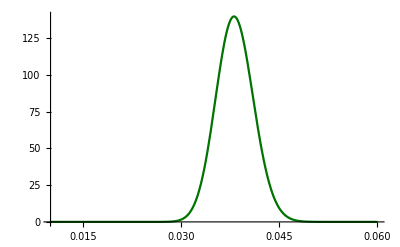

```mathematica
Off[FindMinimum::reged]
ParallelEvaluate[Off[NIntegrate::ncvb]];
datacities=datacitiesr3;
ageQ[x_]:=x≤116;
totyesbins=Table[
casesyes=Select[datacities[[city,3,All,2]],ageQ[#]&];
casesno=Select[datacities[[city,4,All,2]],ageQ[#]&];
{Length[casesno]+Length[casesyes],Length[casesyes]}
,{city,1,Length[datacities]}];
datacities[[All,{3,4}]]=totyesbins;

AbsoluteTiming[
popstate=Total[datacities[[All,-1]]];
fracpop=datacities[[All,-1]]/popstate;
naivep=fracpop.(datacities[[All,4]]/(datacities[[All,3]]+1)); (* +1 to avoid error due to cities with 0 tests *)
{minp,maxp}=Rationalize[{Max[0,naivep-7/100],Min[1,naivep+8/100]},10^-4];

meanvartab=Table[newmeanvarihiprec[datacities[[k,4]],datacities[[k,3]]],{k,1,Length[datacities]}];
meantab=meanvartab[[All,1]];
vartab=meanvartab[[All,2]];
μjoint=meantab.fracpop ; (* μ before displacement *)
varjoint= vartab.fracpop^2;

{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint-p0,V->varjoint};

root=FindRoot[μvarfun[α,β]=={μjoint,varjoint},{α,bestα,bestα/5,5bestα},{β,bestβ,bestβ/5,5bestβ},WorkingPrecision->32];
{bestα,bestβ}=Rationalize[{α/.root,β/.root},10^-9];

norm=1/NIntegrate[beta[p-p0,bestα,bestβ],{p,0,3/10},WorkingPrecision->33];
finalpostbeta[p_]:=norm beta[p,bestα,bestβ];
]
ParallelEvaluate[On[NIntegrate::ncvb]];
pBrazilround3=Plot[finalpostbeta[p-p0],{p,.01,.06},PlotRange->All,PlotStyle->Darker[Green,.55]]
```

```mathematica
ParallelEvaluate[Off[NIntegrate::ncvb]];
ptabBrazilRound3=p2σstatesfun[finalpostbeta,bestα/(bestα+bestβ),μjoint-4 √varjoint-p0,μjoint+4 √varjoint-p0]
ParallelEvaluate[On[NIntegrate::ncvb]];
pBrazil3=Round[Join[ptabBrazilRound3,{bestα,bestβ,√varjoint}],.0001]
errorbrazilRound3=errorfun[{ptabBrazilRound3[[1;;4]]}][[1]]
```

{0.0381,0.0327,0.0439,0.95}

{0.038063003532730079871502612,0.03816584785010786595183421556975,0.032667888683466888998532251,0.043852980727141081728312482,0.949999993791506327657625953}

{0.0381,0.0382,0.0327,0.0439,0.95,292.813,5545.88,0.0029}

Around[3.8063003532730079871502612,{0.5395114849263190872970362,0.578997719441100185680987}]

```mathematica
{1.μjoint+p0,√varjoint}
```

{0.026284,0.00285607243934785253676444870949989585850439}

### Whole country - age bins

```mathematica
Clear[bin]
Monitor[
fatabr3=Table[
Switch[bin,1,ageQ[x_]:=x≤116,2,ageQ[x_]:=x≤29,3,ageQ[x_]:=30≤x≤49,4,ageQ[x_]:=50≤x≤69,5,ageQ[x_]:=x≥70];
datacities=datacitiesr3;
totyesbins=Table[
casesyes=Select[datacities[[city,3,All,2]],ageQ[#]&];
casesno=Select[datacities[[city,4,All,2]],ageQ[#]&];
{Length[casesno]+Length[casesyes],Length[casesyes]}
,{city,1,Length[datacities]}];
datacities[[All,{3,4}]]=totyesbins;

Off[FindMinimum::reged];
ParallelEvaluate[Off[NIntegrate::ncvb]];
popstate=Total[datacities[[All,-1]]];
fracpop=datacities[[All,-1]]/popstate;

meanvartab=Table[newmeanvari3[datacities[[k,4]],datacities[[k,3]]],{k,1,Length[datacities]}];
meantab=meanvartab[[All,1]];vartab=meanvartab[[All,2]];
μjoint=meantab.fracpop ; (* μ before displacement *)
varjoint= vartab.fracpop^2;
{bestα,bestβ}={(-V μ+μ^2-μ^3)/V,((-1+μ) (V-μ+μ^2))/V}/.{μ->μjoint-p0,V->varjoint};

root=FindRoot[μvarfun[α,β]=={μjoint,varjoint},{α,bestα,bestα/5,5bestα},{β,bestβ,bestβ/5,5bestβ},WorkingPrecision->32];
{bestα,bestβ}=Rationalize[{α/.root,β/.root},10^-10];

norm=1/NIntegrate[beta[p-p0,bestα,bestβ],{p,0,5/10},WorkingPrecision->33];
finalpostbeta[p_]:=norm beta[p,bestα,bestβ];

ParallelEvaluate[On[NIntegrate::ncvb]];
Round[{1.μjoint,√varjoint},.000001]
,{bin,1,5}],bin]
Round[fatabr3,.0001]
```

{{0.038217,0.002856},{0.037094,0.004659},{0.049068,0.004971},{0.063837,0.007285},{0.083568,0.012521}}

{{0.0382,0.0029},{0.0371,0.0047},{0.0491,0.005},{0.0638,0.0073},{0.0836,0.0125}}

```mathematica
Round[fatabr1,.00001]
Round[fatabr2,.00001]
Round[fatabr3,.00001]
```

{{0.02627,0.00303},{0.0396,0.00591},{0.04661,0.00657},{0.05088,0.00647},{0.08599,0.01236}}

{{0.0381,0.00304},{0.03685,0.00489},{0.06051,0.00615},{0.05527,0.00692},{0.09258,0.01564}}

{{0.03822,0.00286},{0.03709,0.00466},{0.04907,0.00497},{0.06384,0.00728},{0.08357,0.01252}}

## Analysis

### Analysis Preamble

```mathematica
(*fatabfull=Round[Table[{fatabr1[[i]],fatabr2[[i]],fatabr3[[i]]},{i,1,5}],.00001]
Dimensions[fatabfull]*)
```

```mathematica
fatabfull={{{0.02627,0.00303},{0.0381,0.00304},{0.03822,0.00286}},{{0.0396,0.00591},{0.03685,0.00489},{0.03709,0.00466}},{{0.04661,0.00657},{0.06051,0.00615},{0.04907,0.00497}},{{0.05088,0.00647},{0.05527,0.00692},{0.06384,0.00728}},{{0.08599,0.01236},{0.09258,0.01564},{0.08357,0.01252}}};
```

```mathematica
Clear[ifrcountry,ifr,maxifr]
```

```mathematica
ifrcountry[ifrfun_,ifrmin_,ifrmax_]:=Module[{},
findmax=NMaximize[{ifrfun[x],ifrmin≤x<ifrmax},x];
zmax=findmax[[1]];
xxmax=x/.findmax[[2]];
zrange=Range[zmax/1000,zmax/3,zmax/300];
areatab=Table[
xmintemp=x/.FindRoot[ifrfun[x]==zrange[[j]],{x,9/10xxmax,ifrmin,xxmax}];
xmaxtemp=x/.FindRoot[ifrfun[x]==zrange[[j]],{x,11/10xxmax,xxmax,ifrmax}];
areaunder=NIntegrate[ifrfun[x],{x,xmintemp,xmaxtemp}];
{zrange[[j]],areaunder}
,{j,1,Length[zrange]}
];
areafun=Interpolation[areatab,InterpolationOrder->1];
z95=z/.FindRoot[areafun[z]==95/100,{z,zmax/10,zmax/1000,zmax/3}];
xmin=x/.NMinimize[{(ifrfun[x]-z95)^2,ifrmin<x<xxmax},x][[2]];
xmax=x/.NMinimize[{(ifrfun[x]-z95)^2,xxmax<x<ifrmax},x][[2]];
crosscheck=NIntegrate[ifrfun[x],{x,xmin,xmax}];
{xxmax,xmin,xmax,crosscheck}]
```

### Prevalence Plot in States

```mathematica
(*ptabstatesRound1exact=Import["prob-tab-states-round1-exact-v1.csv","CSV"];
ptabstatesRound2exact=Import["prob-tab-states-round2-exact-v1.csv","CSV"];*)
```

```mathematica
ptabstatesRound1=Import[dir<>"prob-tab-states-FPR1.00%-round1-v6a.csv","CSV"];
ptabstatesRound2=Import[dir<>"prob-tab-states-FPR1.00%-round2-v6a.csv","CSV"];
ptabstatesRound3=Import[dir<>"prob-tab-states-FPR1.00%-round3-v6a.csv","CSV"];
errortabstatesRound1=errormedianfun[ptabstatesRound1];
errortabstatesRound2=errormedianfun[ptabstatesRound2];
errortabstatesRound3=errormedianfun[ptabstatesRound3];
errortabstatesRound1=errorfun[ptabstatesRound1];
errortabstatesRound2=errorfun[ptabstatesRound2];
errortabstatesRound3=errorfun[ptabstatesRound3];
```

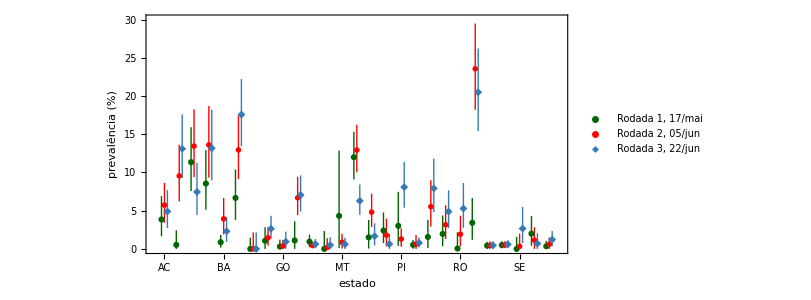

```mathematica
(* In Round 1 PB was not covered *)
ϵ=.2;
errortabstatesRound1b=Thread[{Range[1,27]-ϵ,errortabstatesRound1}];
errortabstatesRound2b=Thread[{Range[1,27]+0,errortabstatesRound2}];
errortabstatesRound3b=Thread[{Range[1,27]+ϵ,errortabstatesRound3}];
lpstatesRoundPT=ListPlot[{errortabstatesRound1b,errortabstatesRound2,errortabstatesRound3b},Frame->True,ImageSize->600,PlotRange->{{.3,27.7},{0,30}},FrameStyle->22,FrameLabel->{"estado","prevalência  (%)"},PlotStyle->{Darker[Green,.6],Red,color1},
IntervalMarkersStyle->{Darker[Green,.6],Red,color1},PlotMarkers->{Automatic,"OpenMarkers",Automatic},FrameTicks->{Table[{i,Style[statesnames[[i]],17,FontFamily->"Economica"]},{i,Length[statesnames]}],Automatic},FrameTicksStyle->20,AspectRatio->.50,PlotLegends->Placed[{Style["Rodada 1, 17/mai",18],Style["Rodada 2, 05/jun",18],Style["Rodada 3, 22/jun",18]},{.5,.82}]]
```

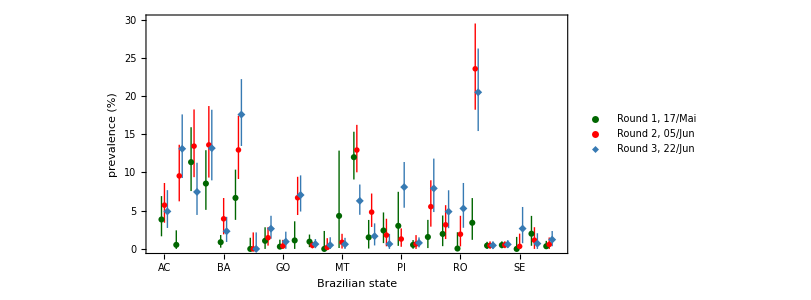

```mathematica
ϵ=.2;
errortabstatesRound1b=Thread[{Range[1,27]-ϵ,errortabstatesRound1}];
errortabstatesRound2b=Thread[{Range[1,27]+0,errortabstatesRound2}];
errortabstatesRound3b=Thread[{Range[1,27]+ϵ,errortabstatesRound3}];
lpstatesRoundEN=ListPlot[{errortabstatesRound1b,errortabstatesRound2,errortabstatesRound3b},Frame->True,ImageSize->600,PlotRange->{{.3,27.7},{0,30}},FrameStyle->22,FrameLabel->{"Brazilian state","prevalence  (%)"},PlotStyle->{Darker[Green,.6],Red,color1},
IntervalMarkersStyle->{Darker[Green,.6],Red,color1},PlotMarkers->{Automatic,"OpenMarkers",Automatic},FrameTicks->{Table[{i,Style[statesnames[[i]],17,FontFamily->"Economica"]},{i,Length[statesnames]}],Automatic},FrameTicksStyle->20,AspectRatio->.50,PlotLegends->Placed[{Style["Round 1, 17/Mai",18],Style["Round 2, 05/Jun",18],Style["Round 3, 22/Jun",18]},{.5,.82}]]
```

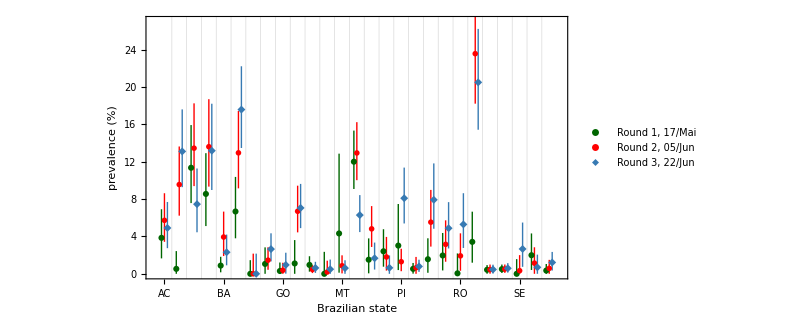

```mathematica
ϵ=.2;
errortabstatesRound1b=Thread[{Range[1,27]-ϵ,errortabstatesRound1}];
errortabstatesRound2b=Thread[{Range[1,27]+0,errortabstatesRound2}];
errortabstatesRound3b=Thread[{Range[1,27]+ϵ,errortabstatesRound3}];
lpstatesRoundENalt=ListPlot[{errortabstatesRound1b,errortabstatesRound2,errortabstatesRound3b},Frame->True,ImageSize->600,PlotRange->{{.3,27.7},{0,27}},FrameStyle->24,FrameLabel->{"Brazilian state","prevalence  (%)"},PlotStyle->{Darker[Green,.6],Red,color1},
IntervalMarkersStyle->{Darker[Green,.6],Red,color1},PlotMarkers->{Automatic,"OpenMarkers",Automatic},FrameTicks->{Automatic,{Table[{i,If[OddQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}],Table[{i,If[EvenQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}]}},FrameTicksStyle->22,AspectRatio->.55,PlotLegends->Placed[{Style["Round 1, 17/Mai",20],Style["Round 2, 05/Jun",20],Style["Round 3, 22/Jun",20]},{.498,.82}],
GridLines->{Range[1.5,26.5,1],None},GridLinesStyle->Lighter[Gray,.7]]
```

```mathematica
(*ϵ=.2;
errortabstatesRound1b=Thread[{Range[1,27]-ϵ,errortabstatesRound1}];
errortabstatesRound2b=Thread[{Range[1,27]+0,errortabstatesRound2}];
errortabstatesRound3b=Thread[{Range[1,27]+ϵ,errortabstatesRound3}];
lpstatesRoundENalt2=ListPlot[{errortabstatesRound1b,errortabstatesRound2,errortabstatesRound3b},Frame->True,ImageSize->600,PlotRange->{{.3,27.7},{0,27}},FrameStyle->24,FrameLabel->{None,"prevalence  (%)"},PlotStyle->{Darker[Green,.6],Red,color1},
IntervalMarkersStyle->{Darker[Green,.6],Red,color1},PlotMarkers->{Automatic,"OpenMarkers",Automatic},FrameTicks->{Automatic,{Table[{i,If[1>2,Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}],Table[{i,If[EvenQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}]}},FrameTicksStyle->22,AspectRatio->.55,PlotLegends->Placed[{Style["Round 1, 17/Mai",20],Style["Round 2, 05/Jun",20],Style["Round 3, 22/Jun",20]},{.498,.82}],
GridLines->{Range[1.5,26.5,1],None},GridLinesStyle->Lighter[Gray,.7]]*)
```

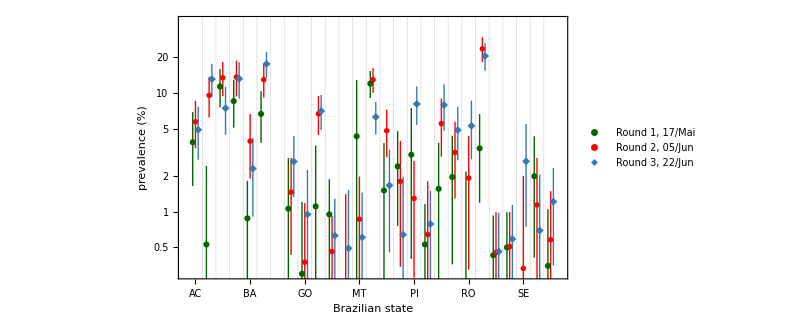

```mathematica
ϵ=.2;
errortabstatesRound1b=Thread[{Range[1,27]-ϵ,errortabstatesRound1}];
errortabstatesRound2b=Thread[{Range[1,27]+0,errortabstatesRound2}];
errortabstatesRound3b=Thread[{Range[1,27]+ϵ,errortabstatesRound3}];
lpstatesRoundENlog=ListLogPlot[{errortabstatesRound1b,errortabstatesRound2,errortabstatesRound3b},Frame->True,ImageSize->600,PlotRange->{{.3,27.7},{.3,40}},FrameStyle->24,FrameLabel->{"Brazilian state","prevalence  (%)"},PlotStyle->{Darker[Green,.6],Red,color1},
IntervalMarkersStyle->{Darker[Green,.6],Red,color1},PlotMarkers->{Automatic,"OpenMarkers",Automatic},FrameTicks->{Automatic,{Table[{i,If[OddQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}],Table[{i,If[EvenQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}]}},FrameTicksStyle->22,AspectRatio->.55,PlotLegends->Placed[{Style["Round 1, 17/Mai",20],Style["Round 2, 05/Jun",20],Style["Round 3, 22/Jun",20]},{.498,.82}],
GridLines->{Range[1.5,26.5,1],None},GridLinesStyle->Lighter[Gray,.7]]
```

```mathematica
Table[{i,Style[statesnames[[i]],17,FontFamily->"Economica"]},{i,1,Length[statesnames],2}]
```

{{1,AC},{3,AM},{5,BA},{7,DF},{9,GO},{11,MG},{13,MT},{15,PB},{17,PI},{19,RJ},{21,RO},{23,RS},{25,SE},{27,TO}}

```mathematica
Export["state-prevalence-FPR1-PT.pdf",lpstatesRoundPT]
Export["state-prevalence-FPR1-EN.pdf",lpstatesRoundEN]
Export["state-prevalence-FPR1-EN-log.pdf",lpstatesRoundENlog]
Export["state-prevalence-FPR1-EN-alt.pdf",lpstatesRoundENalt]
(*Export["state-prevalence-FPR1-EN-alt2.pdf",lpstatesRoundENalt2]*)
```

state-prevalence-FPR1-PT.pdf

state-prevalence-FPR1-EN.pdf

state-prevalence-FPR1-EN-log.pdf

state-prevalence-FPR1-EN-alt.pdf

### IFR as inverse of a Beta marg. fading IGG

```mathematica
DFnyes=datacities3rounds[[27,6;;8]]
DFntot=datacities3rounds[[27,3;;5]]
```

{0,2,2}

{240,250,250}

```mathematica
runtab={"501","502","503","504","505"};agename="_AgeBin5";
disttab=Table[0,{run,runtab}];
```

```mathematica
βshift=p0;
invbeta[pd_,α_,β_,x_]:=Piecewise[{{(pd (pd/x-βshift)^α (1-pd/x+βshift)^β Gamma[α+β])/((pd-x βshift) (pd-x (1+βshift)) (-1+BetaRegularized[-βshift,α,β]) Gamma[α] Gamma[β]),pd<x+x βshift},{0,pd≥x+x βshift}}];
invbetaCDFfull[pd_,α_,β_,x_]:=Piecewise[{{(-Gamma[α] Gamma[β]+Beta[pd/x-βshift,α,β] Gamma[α+β])/((-1+BetaRegularized[-βshift,α,β]) Gamma[α] Gamma[β]),pd<x+x βshift}},0];
invbetaCDF[pd_,α_,β_,x_]:=(-Gamma[α] Gamma[β]+Beta[pd/x-βshift,α,β] Gamma[α+β])/((-1+BetaRegularized[-βshift,α,β]) Gamma[α] Gamma[β]); (* x > pd/(1+βshift) *)
```

```mathematica
ptabstatesRound1=Import[dir<>"prob-tab-states-FPR1.00%-round1-v6a.csv","CSV"];
ptabstatesRound2=Import[dir<>"prob-tab-states-FPR1.00%-round2-v6a.csv","CSV"];
ptabstatesRound3=Import[dir<>"prob-tab-states-FPR1.00%-round3-v6a.csv","CSV"];
```

```mathematica
invbetapdftab=Table[
cdf[x_]=invbetaCDF[pdvec[[i]],αtab[[i]],βtab[[i]],x];
xmedian=x/.FindRoot[cdf[x]==50/100,{x,IFRvec[[i]],2 10^-4,1},PrecisionGoal->5,AccuracyGoal->5];
pdf[x_]=invbeta[pdvec[[i]],αtab[[i]],βtab[[i]],x];
Simplify[pdf[x],x>pdvec[[i]]/(1+βshift)]
,{i,1,Length[ptabstatesRoundX]}];
```

```mathematica
Monitor[
Do[
ptabstatesRoundX=Import[dir<>"prob-tab-states-FPR1.00%-round"<>ToString[round]<>"-v6a.csv","CSV"];
αtab=ptabstatesRoundX[[All,6]];
βtab=ptabstatesRoundX[[All,7]];
(*Print[1.{αtab[[7]],βtab[[7]]}];*)
αtab[[7]]=DFnyes[[round]]+1.001; βtab[[7]]=DFntot[[round]](1-FNR-FPR)-DFnyes[[round]]+1.; 
(*Print[1.{αtab[[7]],βtab[[7]]}];*) (* DF has only 1 city -- city approx is better *)
IFRtab=Table[
xlowerlimitmarg=1;
k=0;
Do[
k++;
valedata=Import["results\\run"<>run<>"\\"<>run<>"-ztab-a2-m2-f"<>ToString[round]<>".txt","CSV"];
pdvec=valedata[[2;;All,8]];
IFRvec=valedata[[2;;All,4]];
xlowerlimit=pdvec[[i]]/(1+βshift);
(*CDFtab[[i]]=Simplify[invbetaCDF[pdvec[[i]],αtab[[i]],βtab[[i]],x],x>xlowerlimit];*)
pdftemp[x_]=Simplify[invbeta[pdvec[[i]],αtab[[i]],βtab[[i]],x],x>xlowerlimit];
disttab[[k]]=pdftemp[x];
xlowerlimitmarg=20/10Min[xlowerlimitmarg,xlowerlimit];
,{run,runtab}];
pdf[x_]=(1/5)Sum[disttab[[k]],{k,1,Length[disttab]}];
xlowerlimit=xlowerlimitmarg;

findmax=NMaximize[{pdf[x],xlowerlimit≤x<3/10},x];
zmax=findmax[[1]];
xxmax=x/.findmax[[2]];

xmedianfun[y_]:=NIntegrate[pdf[x],{x,xlowerlimit,y}];
(* will give an error msg, which can be ignored *)
xmedian=y/.FindRoot[xmedianfun[y]==1/2,{y,xxmax,3/4xxmax,3/10}];

zrange=Range[zmax/1000,zmax/4,zmax/300];
areatab=Table[
xmintemp=x/.FindRoot[pdf[x]==zrange[[j]],{x,6/10xxmax,xlowerlimit,xxmax}];
xmaxtemp=x/.FindRoot[pdf[x]==zrange[[j]],{x,16/10xxmax,xxmax,1}];
areaunder=NIntegrate[pdf[x],{x,xmintemp,xmaxtemp},PrecisionGoal->5,AccuracyGoal->5];
{zrange[[j]],areaunder}
,{j,1,Length[zrange]}
];

areafun=Interpolation[areatab,InterpolationOrder->1];
z95=z/.FindRoot[areafun[z]==95/100,{z,zmax/10,zmax/1000,zmax/4}];
xmin=x/.NMinimize[{(pdf[x]-z95)^2,xlowerlimit<x<xxmax},x][[2]];
xmax=x/.NMinimize[{(pdf[x]-z95)^2,xxmax<x<1},x][[2]];
crosscheck=NIntegrate[pdf[x],{x,xmin,xmax}];
If[.945<crosscheck<.955,Null,Print["crosscheck error!  i = "<>ToString[i]<>"; Round = "<>ToString[round]<>";  CI = "<>ToString[crosscheck]<>";"]];

(*Print[{i,xmedian,xmin,xmax}];*)
{statesnames[[i]],xxmax,xmedian,xmin,xmax,crosscheck}
,{i,1,Length[ptabstatesRoundX]}];
Export["IFR-95CI-MQ-round"<>ToString[round]<>"-40-80days-v6a.txt",IFRtab,"CSV"]
,{round,1,3}],
{round,i}]
```

NIntegrate::nlim: x = y is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

FindRoot::reged: The point {1.} is at the edge of the search region {0.0188012,1.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {1.} is at the edge of the search region {0.0498052,1.} in coordinate 1 and the computed search direction points outside the region.

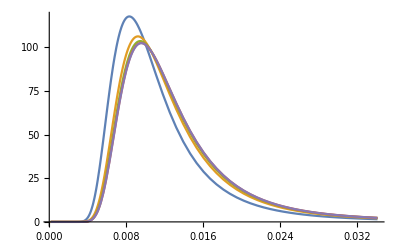

```mathematica
Plot[disttab,{x,0,3xmedian},PlotRange->All]
```

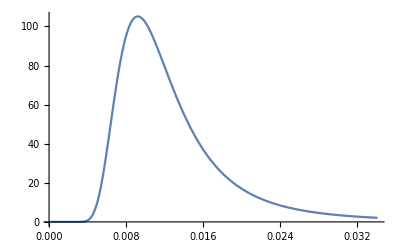

{105.096,{x→0.00922386}}

0.0113837

{0.00465524,0.0276057}

0.949995

```mathematica
Plot[pdf[x],{x,0,3xmedian},PlotRange->All]
findmax
xmedian
{xmin,xmax}
crosscheck
```

### IFR as inverse of a Beta, whole country, different T (fading IGG), age bins

```mathematica
Dimensions[fatabfull]
Round[100fatabfull,.01][[All,All,1]]
```

{5,3,2}

{{2.63,3.81,3.82},{3.96,3.68,3.71},{4.66,6.05,4.91},{5.09,5.53,6.38},{8.6,9.26,8.36}}

```mathematica
maxifr=0.1;
```

```mathematica
(*data=Import["results\\run202\\202-ftab-a1-b1-m2-f1.txt","TSV"]
data[[All,7]]*)
```

```mathematica
(*fatab={0.0259,0.03801,0.0381};
σfatab={0.0030,0.00301,0.002826};*)
```

```mathematica
runtab={"201","202","203"};
runtab={"306","307","308","309","310"};
runtab={"301","302","303","304","305"};
runtab={"601","602","603","604","605"};agename="_AgeBin1";
runtab={"501","502","503","504","505"};agename="_AgeBin5";

distrounds=Table[-1,{3}];
distTtab=Table[-1,{run,runtab},{agebin,5}];
distTtabfull=Table[-1,{run,runtab},{agebin,5},{round,3}];
```

```mathematica
Monitor[
Do[
Do[
Do[
run=runtab[[irun]];
datafd=ToExpression[Import["results\\run"<>run<>"\\"<>run<>"-ztab-a1-m2-f"<>ToString[round]<>agename<>".txt","CSV"]];
fd=datafd[[2,1+agebin,8-1]];σfd=Max[10.^-8,datafd[[2,1+agebin,13-1]] fd];
{fa,σfa}=fatabfull[[agebin,round]];
distrounds[[round]]=TransformedDistribution[y/x,{x\[Distributed]NormalDistribution[fa,σfa],y\[Distributed]NormalDistribution[fd,σfd]}];
ifr=fd/fa;
σifr=√((σfd/fa)^2+(σfa fd/fa^2)^2);
Print[{run,agebin,irun,fd,σfd,(σfa/fa)/(σfd/fd)}];
distTtabfull[[irun,agebin,round]]=PDF[distrounds[[round]],x];
,{round,3}];
{ifrmin,ifrmax}={.0001,.03};
 If[agebin==2,{ifrmin,ifrmax}={10.^-5,.01}];
 If[agebin==4,{ifrmin,ifrmax}={.002,.03}];If[agebin==5,{ifrmin,ifrmax}={.01,.07}];
ifr123[x_]=PDF[distrounds[[1]],x]PDF[distrounds[[2]],x]PDF[distrounds[[3]],x];
norm=1/NIntegrate[ifr123[x],{x,ifrmin,ifrmax}];
ifr123[x_]=norm ifr123[x];
distTtab[[irun,agebin]]=ifr123[x];

(*pdfmarg[x_]:=Sum[PDF[disttab[[i]],x],{i,1,Length[disttab]}];*)
(*map=ParallelMap[{#,pdfmarg[#]}&,Range[.004,maxifr,.0001*5]];
ifrfuntemp=Interpolation[map];
norm=1/NIntegrate[ifrfuntemp[x],{x,.004,maxifr}];*)

,{irun,Length[runtab]}];
,{agebin,1,5}];

,{agebin,run,round}]
```

{501,1,1,0.000246024,5.12681×10^-6,5.53494}

{501,1,1,0.000315836,2.0447×10^-6,12.3249}

{501,1,1,0.000322125,7.73877×10^-7,31.1478}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{502,1,2,0.000257286,5.89332×10^-6,5.03546}

{502,1,2,0.000347089,3.25758×10^-6,8.50148}

{502,1,2,0.000370916,1.42318×10^-7,195.025}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{503,1,3,0.000265349,7.12865×10^-6,4.29332}

{503,1,3,0.000371836,4.61011×10^-6,6.4356}

$Aborted

```mathematica
Dimensions[distTtabfull]
distTtabfull[[1,1,1]]
Export["distTtabfull-tauad=0.tab",distTtabfull,"List"]
```

{5,5,3}

(8.72213174421248×10^-82102693 √(5.32782×10^10+4.89142×10^21 x^2)+2.09361704217474×10^-82102707 ⅇ^((7.336×10^-30 (5.22453×10^20+3.55038×10^29 x)^2)/(5.32782×10^10+4.89142×10^21 x^2)) (5.22453×10^20+3.55038×10^29 x) (1.+Erf[(1.41507×10^6+9.61621×10^14 x)/(√(5.32782×10^10+4.89142×10^21 x^2))])-2.09361704217474×10^-82102707 ⅇ^((7.336×10^-30 (5.22453×10^20+3.55038×10^29 x)^2)/(5.32782×10^10+4.89142×10^21 x^2)) (5.22453×10^20+3.55038×10^29 x) Erfc[(1.41507×10^6+9.61621×10^14 x)/(√(5.32782×10^10+4.89142×10^21 x^2))])/(5.32782×10^10+4.89142×10^21 x^2)^(3/2)

distTtabfull-tauad=0.tab

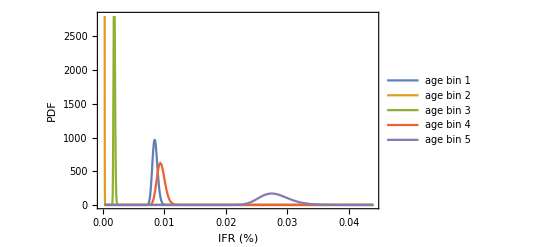

```mathematica
Plot[Evaluate[distTtab[[1,All]]],{x,.0003,.044},PlotRange->{0,2800},Frame->True,FrameStyle->16,FrameLabel->{"IFR (%)","PDF"},PlotStyle->Thick,PlotLegends->{"age bin 1","age bin 2","age bin 3","age bin 4","age bin 5"}]
Plot[Evaluate[distTtab[[3,All]]],{x,.0003,.003},PlotRange->{0,2800},Frame->True,FrameStyle->16,FrameLabel->{"IFR (%)","PDF"},PlotStyle->Thick,PlotLegends->{"age bin 1","age bin 2","age bin 3","age bin 4","age bin 5"}]
```

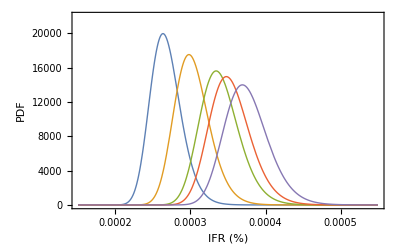

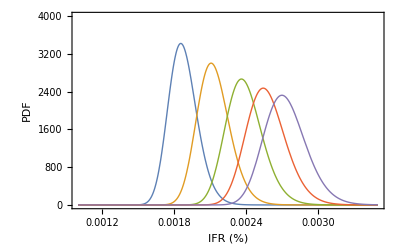

```mathematica
Plot[Evaluate[distTtab[[All,2]]],{x,.00015,.00055},PlotRange->{0,22000},Frame->True,FrameStyle->16,FrameLabel->{"IFR (%)","PDF"},PlotStyle->Thick]
Plot[Evaluate[distTtab[[All,3]]],{x,.001,.0035},PlotRange->{0,4000},Frame->True,FrameStyle->16,FrameLabel->{"IFR (%)","PDF"},PlotStyle->Thick]
```

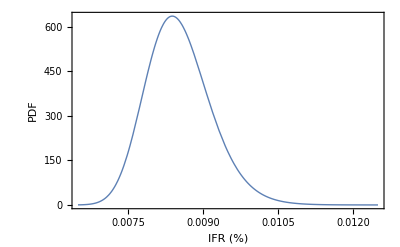

```mathematica
Plot[distTtabfull[[1,1,3]],{x,.0065,.0125},PlotRange->All,Frame->True,FrameStyle->16,FrameLabel->{"IFR (%)","PDF"},PlotRange->All,PlotStyle->Thick]
```

```mathematica
{ifrmin,ifrmax}={.0001,.015}
Monitor[ifrTtabfull=Table[
Δifr=3. 10^-5;
If[agebin==1,{ifrmin,ifrmax}={10.^-3,.018}];
If[agebin==2,{ifrmin,ifrmax,Δifr}={10.^-4,.0006,2 10^-6}];If[agebin==3,{ifrmin,ifrmax,Δifr}={10.^-3,.004,5 10^-6}];
If[agebin==4,{ifrmin,ifrmax}={.001,.018}];If[agebin==5,{ifrmin,ifrmax,Δifr}={.015,.055,.0002}];
funtemp[x_]=distTtab[[run,agebin]];
ifr123map=ParallelMap[{#,funtemp[#]}&,Range[ifrmin,ifrmax,Δifr]];
ifr123fun=Interpolation[ifr123map];
ifrcountry[ifr123fun,ifrmin,ifrmax]
,{run,1,5},{agebin,1,1}],{run,agebin}]
MinMax[ifrTtabfull[[All,All,-1]]]
```

{0.0001,0.015}

{{{0.00787486,0.00718831,0.00870565,0.950001}},{{0.00862319,0.00786967,0.00953547,0.950001}},{{0.00925265,0.0084415,0.0102353,0.95}},{{0.0096377,0.00879078,0.0106641,0.950001}},{{0.00990797,0.00903535,0.010966,0.950002}}}

{0.95,0.950002}

```mathematica
ifrTtabfulltauad0={{{0.00787486,0.00718831,0.00870565,0.95}},{{0.00862319,0.00786967,0.00953547,0.95}},{{0.00925265,0.0084415,0.0102353,0.95}},{{0.0096377,0.00879078,0.0106641,0.95}},{{0.00990797,0.00903535,0.010966,0.95}}};
```

```mathematica
ifrTtabfull={{{0.00843747,0.00769721,0.0093321,0.950001},{0.000263306,0.000229126,0.000309185,0.95},{0.0018567,0.00165283,0.0021168,0.950001},{0.00936129,0.00824863,0.0108135,0.950002},{0.0274781,0.0235126,0.0330095,0.950001}},{{0.00936858,0.00854682,0.0103615,0.950001},{0.000297912,0.000258967,0.000350193,0.95},{0.00210932,0.00187717,0.00240562,0.950001},{0.0104,0.00916501,0.0120124,0.950001},{0.0305252,0.0260984,0.0367132,0.950001}},{{0.0102493,0.00934811,0.011338,0.950002},{0.00033416,0.000290536,0.000392925,0.95},{0.00236206,0.0021007,0.00269588,0.950001},{0.0113669,0.010015,0.0131322,0.950001},{0.0332616,0.028419,0.0400474,0.95}},{{0.0108109,0.00985812,0.011962,0.950002},{0.000347772,0.000302233,0.000409172,0.95},{0.00254336,0.00226184,0.00290353,0.950001},{0.0120444,0.0106098,0.0139191,0.950004},{0.0349478,0.029836,0.0421238,0.95}},{{0.0112656,0.0102687,0.01247,0.950002},{0.000369198,0.000320566,0.000434874,0.950001},{0.00269924,0.00239969,0.0030831,0.950001},{0.0125657,0.0110654,0.0145273,0.950001},{0.0363471,0.0310054,0.0438566,0.95}}}
```

```mathematica
ifrTtab=ifrTtabfull[[All,All,{1,2,3}]]
```

{{{0.00843747,0.00769721,0.0093321},{0.000263306,0.000229126,0.000309185},{0.0018567,0.00165283,0.0021168},{0.00936129,0.00824863,0.0108135},{0.0274781,0.0235126,0.0330095}},{{0.00936858,0.00854682,0.0103615},{0.000297912,0.000258967,0.000350193},{0.00210932,0.00187717,0.00240562},{0.0104,0.00916501,0.0120124},{0.0305252,0.0260984,0.0367132}},{{0.0102493,0.00934811,0.011338},{0.00033416,0.000290536,0.000392925},{0.00236206,0.0021007,0.00269588},{0.0113669,0.010015,0.0131322},{0.0332616,0.028419,0.0400474}},{{0.0108109,0.00985812,0.011962},{0.000347772,0.000302233,0.000409172},{0.00254336,0.00226184,0.00290353},{0.0120444,0.0106098,0.0139191},{0.0349478,0.029836,0.0421238}},{{0.0112656,0.0102687,0.01247},{0.000369198,0.000320566,0.000434874},{0.00269924,0.00239969,0.0030831},{0.0125657,0.0110654,0.0145273},{0.0363471,0.0310054,0.0438566}}}

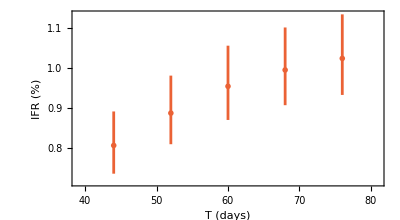

```mathematica
colors=ColorData[97,"ColorList"];
Tvec=Range[44.,80,8]
ifrTwitherrors=Table[{Tvec[[j]],100Around[ifrTtab[[j,1]],ifrTtab[[j,2;;3]]-ifrTtab[[j,1]]]},{j,Length[ifrTtab]}]
lplotT=ListPlot[ifrTwitherrors,Frame->True,FrameStyle->16,AspectRatio->.55,FrameLabel->{"T (days)","IFR (%)"},PlotRange->{{39,81},All},PlotStyle->{Thick,colors[[4]]},PlotMarkers->"OpenMarkers",IntervalMarkersStyle->{Thickness[.005],colors[[4]]}]
```

```mathematica
Export["IFR-vs-T.pdf",lplotT]
```

IFR-vs-T.pdf

```mathematica
NotebookSave[]
```

### IFR as inverse of a Beta, whole country, different T, τad=0 (fading IGG)

```mathematica
maxifr=0.017;
```

```mathematica
(*data=Import["results\\run202\\202-ftab-a1-b1-m2-f1.txt","TSV"]
data[[All,7]]*)
```

```mathematica
fatab={0.0259,0.03801,0.0381};
σfatab={0.0030,0.00301,0.002826};
runtab={"201","202","203"};
runtab={"401","402","403","404","405"};
runtab={"601","602","603","604","605"};ioffset=-1;

distrounds=Table[-1,{3}];
distTtab=Table[-1,{run,runtab}];
```

```mathematica
i=0;
Monitor[
Do[
i++;
Do[
datafd=ToExpression[Import["results\\run"<>run<>"\\"<>run<>"-ztab-a1-m2-f"<>ToString[round]<>"_AgeBin1.txt","CSV"]];
fd=datafd[[2,2,8-1]];σfd=Max[10.^-8,datafd[[2,2,13-1]] fd];
(*datafd=ToExpression[Import["results\\run"<>run<>"\\"<>run<>"-ztab-a1-m2-f"<>ToString[round]<>".txt","CSV"]];
fd=datafd[[2,8]];σfd=Max[10.^-8,datafd[[2,13]] fd];*)
fa=fatab[[round]];σfa=σfatab[[round]];
distrounds[[round]]=TransformedDistribution[y/x,{x\[Distributed]NormalDistribution[fa,σfa],y\[Distributed]NormalDistribution[fd,σfd]}];
ifr=fd/fa;
σifr=√((σfd/fa)^2+(σfa fd/fa^2)^2);
Print[{run,i,fd,σfd,(σfa/fa)/(σfd/fd)}];
,{round,3}];

ifr123[x_]=PDF[distrounds[[1]],x]PDF[distrounds[[2]],x]PDF[distrounds[[3]],x];
norm=1/NIntegrate[ifr123[x],{x,.004,.02}];
ifr123[x_]=norm ifr123[x];
distTtab[[i]]=ifr123[x];

,{run,runtab}];

,{run,round}]
```

{601,1,0.000194447,1.×10^-8,2252.28}

{601,1,0.00029122,1.×10^-8,2306.16}

{601,1,0.000324026,1.×10^-8,2403.4}

$Aborted

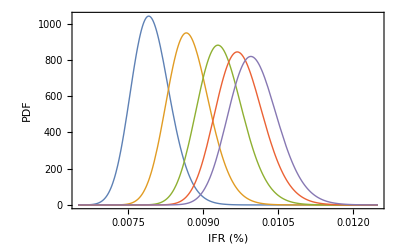

```mathematica
(* new, with smoothing of 20 days *)
Plot[distTtab,{x,.0065,.0125},PlotRange->All,Frame->True,FrameStyle->16,FrameLabel->{"IFR (%)","PDF"},PlotRange->All,PlotStyle->Thick]
```

```mathematica
ifrTtabfull2=Table[
funtemp[x_]=distTtab[[j]];
ifr123map=ParallelMap[{#,funtemp[#]}&,Range[.004,maxifr,.0001]];
ifr123fun=Interpolation[ifr123map];
ifrcountry[ifr123fun],{j,1,Length[distTtab]}]
ifrTtab2=ifrTtabfull2[[All,{1,3,4}]]
```

{{0.00791322,0.011579,0.00722806,0.00874379,0.950002},{0.00866688,0.011579,0.00791311,0.00957695,0.950001},{0.00929976,0.011579,0.00848786,0.0102793,0.950001},{0.00968617,0.011579,0.0088389,0.0107096,0.950001},{0.00995706,0.011579,0.00908492,0.0110129,0.950001}}

{{0.00791322,0.00722806,0.00874379},{0.00866688,0.00791311,0.00957695},{0.00929976,0.00848786,0.0102793},{0.00968617,0.0088389,0.0107096},{0.00995706,0.00908492,0.0110129}}

```mathematica
ifrTtab2old={{0.00746893,0.00681661,0.00825618},{0.00806103,0.00735478,0.00891509},{0.00854429,0.00779361,0.0094545},{0.00880368,0.00802941,0.00974479},{0.00898864,0.0081946,0.00994937}};
ifrTtab2={{0.00791322,0.00722806,0.00874379},{0.00866688,0.00791311,0.00957695},{0.00929976,0.00848786,0.0102793},{0.00968617,0.0088389,0.0107096},{0.00995706,0.00908492,0.0110129}};
```

### IFR as inverse of a Beta, whole country, marg. T (fading IGG)

```mathematica
fatab={0.0259,0.03801,0.0381};
σfatab={0.0030,0.00301,0.002826};
runtab={"201","202","203"};
runtab={"306","307","308","309","310"};
runtab={"301","302","303","304","305"};
runtab={"501","502","503","504","505"};
disttab=Table[0,{run,runtab}];
```

```mathematica
Monitor[
Do[i=0;
Do[
i++;
datafd=Import["results\\run"<>run<>"\\"<>run<>"-ztab-a1-m2-f"<>ToString[round]<>".txt","CSV"];
fd=datafd[[2,8]];σfd=Max[10.^-8,datafd[[2,13]] fd];
fa=fatab[[round]];σfa=σfatab[[round]];
disttab[[i]]=TransformedDistribution[y/x,{x\[Distributed]NormalDistribution[fa,σfa],y\[Distributed]NormalDistribution[fd,σfd]}];
ifr=fd/fa;
σifr=√((σfd/fa)^2+(σfa fd/fa^2)^2);
Print[{run,i,fd,σfd,(σfa/fa)/(σfd/fd)}];
,{run,runtab}];
pdfmarg[x_]:=Sum[PDF[disttab[[i]],x],{i,1,Length[disttab]}]; (* marginalization *)
map=ParallelMap[{#,pdfmarg[#]}&,Range[.004,maxifr,.0001]];
ifrfuntemp=Interpolation[map];
norm=1/NIntegrate[ifrfuntemp[x],{x,.004,maxifr}];
Switch[round,1,ifrfun1[x_]=norm *ifrfuntemp[x],2,ifrfun2[x_]=norm *ifrfuntemp[x],3,ifrfun3[x_]=norm *ifrfuntemp[x]]
,{round,3}]
,{run,round}]
ifr123[x_]=ifrfun1[x]ifrfun2[x]ifrfun3[x];
norm=1/NIntegrate[ifr123[x],{x,.004,.02}];
ifr123[x_]=norm ifr123[x];
```

{301,1,0.000204449,5.89748×10^-6,4.01549}

{302,2,0.000211492,6.25244×10^-6,3.91802}

{303,3,0.000215495,7.08578×10^-6,3.52267}

{304,4,0.000215495,7.08578×10^-6,3.52267}

{305,5,0.000215495,7.08578×10^-6,3.52267}

{301,1,0.000298282,3.91124×10^-6,6.03922}

{302,2,0.000320753,4.84313×10^-6,5.2446}

{303,3,0.000335282,5.84295×10^-6,4.54409}

{304,4,0.00034423,6.37969×10^-6,4.27285}

{305,5,0.000350453,6.91261×10^-6,4.01473}

{301,1,0.000325711,2.3632×10^-7,102.23}

{302,2,0.000369571,1.13855×10^-6,24.0765}

{303,3,0.000408281,3.01859×10^-6,10.0324}

{304,4,0.000432122,3.71319×10^-6,8.63188}

{305,5,0.000449466,5.33395×10^-6,6.25022}

```mathematica
ifrcountry[ifr123]
ifrcountry[ifrfun1]
ifrcountry[ifrfun2]
ifrcountry[ifrfun3]
```

{0.00854481,0.011797,0.00761427,0.00992997,0.950001}

{0.00799526,0.011797,0.00641518,0.0104325,0.950001}

{0.00865208,0.011797,0.00704804,0.0104405,0.950001}

{0.0109964,0.011797,0.00774414,0.0129733,0.95}

```mathematica
NotebookSave[]
```

```mathematica
colors=ColorData[97,"ColorList"];
pifr=Plot[{ifrfun1[x/100],ifrfun2[x/100],ifrfun3[x/100],ifr123[x/100]},{x,.6,1.34},Frame->True,FrameStyle->16,FrameLabel->{"IFR (%)","PDF"},PlotRange->All,PlotStyle->Thick];
sifr=Show[pifr,
Graphics[Text[Style["Round 1",16,colors[[1]]],{.69,480}]],Graphics[Text[Style["Round 2",16,colors[[2]]],{.98,455}]],Graphics[Text[Style["Round 3",16,colors[[3]]],{1.11,340}]],Graphics[Text[Style["average",16,colors[[4]]],{.95,720}]]]
(*Export["brazil-ifr-plot-marg-40-80-days-tau0.pdf",sifr]*)
```

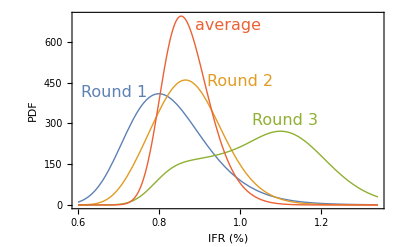

brazil-ifr-plot-marg-40-80-days.pdf

```mathematica
colors=ColorData[97,"ColorList"];
pifr=Plot[{ifrfun1[x/100],ifrfun2[x/100],ifrfun3[x/100],ifr123[x/100]},{x,.6,1.34},Frame->True,FrameStyle->16,FrameLabel->{"IFR (%)","PDF"},PlotRange->All,PlotStyle->Thick];
sifr=Show[pifr,
Graphics[Text[Style["Round 1",16,colors[[1]]],{.69,415}]],Graphics[Text[Style["Round 2",16,colors[[2]]],{1.,455}]],Graphics[Text[Style["Round 3",16,colors[[3]]],{1.11,310}]],Graphics[Text[Style["average",16,colors[[4]]],{.97,660}]]]
Export["brazil-ifr-plot-marg-40-80-days.pdf",sifr]
```

### IFR as inverse of a Beta, whole country, marg. T (fading IGG), age bins

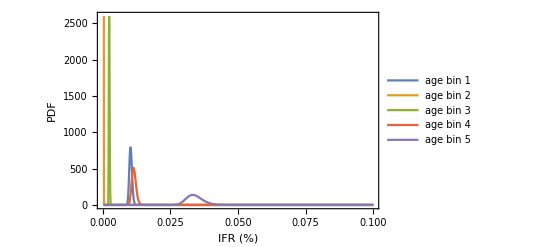

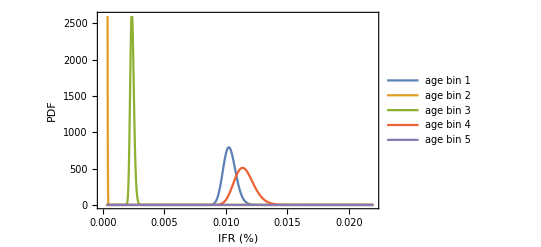

```mathematica
Plot[Evaluate[distTtab[[3,All]]],{x,.0003,.1},PlotRange->{0,2600},Frame->True,FrameStyle->16,FrameLabel->{"IFR (%)","PDF"},PlotRange->All,PlotStyle->Thick,PlotLegends->{"age bin 1","age bin 2","age bin 3","age bin 4","age bin 5"}]
Plot[Evaluate[distTtab[[3,All]]],{x,.0003,.022},PlotRange->{0,2600},Frame->True,FrameStyle->16,FrameLabel->{"IFR (%)","PDF"},PlotRange->All,PlotStyle->Thick,PlotLegends->{"age bin 1","age bin 2","age bin 3","age bin 4","age bin 5"}]
```

```mathematica
Monitor[ifrmargTtab=Table[
{ifrmin,ifrmax,Δifr}={.0001,.03,.00007};
If[agebin==2,{ifrmin,ifrmax,Δifr}={10.^-5,.01,.00002}];
If[agebin==4,{ifrmin,ifrmax}={.002,.03}];If[agebin==5,{ifrmin,ifrmax,Δifr}={.01,.07,.0003}];

pdfmarg[x_]=Sum[distTtabfull[[i,agebin,round]],{i,1,Length[distTtabfull]}];
map=ParallelMap[{#,pdfmarg[#]}&,Range[ifrmin,ifrmax,Δifr]];
map=Join[map,{{0,0},{10.^-6,0},{3 10.^-6,0},{.08,0},{.085,0},{.9,0}}];
ifrfuntemp=Interpolation[map];
norm=1/NIntegrate[ifrfuntemp[x],{x,ifrmin,ifrmax}];
norm *ifrfuntemp[x],{agebin,1,1},{round,1,3}];
,{agebin,round}]
```

```mathematica
Monitor[ifrmargTroundtab=Table[
{ifrmin,ifrmax,Δifr}={.0001,.03,.00004};
If[agebin==2,{ifrmin,ifrmax,Δifr}={10.^-5,.01,.00002}];
If[agebin==4,{ifrmin,ifrmax}={.002,.03}];If[agebin==5,{ifrmin,ifrmax,Δifr}={.01,.07,.0003}];

pdfmarg1[x_]=(1/5)Sum[distTtabfull[[i,agebin,1]],{i,1,Length[distTtabfull]}];
pdfmarg2[x_]=(1/5)Sum[distTtabfull[[i,agebin,2]],{i,1,Length[distTtabfull]}];
pdfmarg3[x_]=(1/5)Sum[distTtabfull[[i,agebin,3]],{i,1,Length[distTtabfull]}];
pdfmarg[x_]=pdfmarg1[x]pdfmarg2[x]pdfmarg3[x];
map=Map[{#,pdfmarg[#]}&,Range[ifrmin,ifrmax,Δifr]];
map=Join[map,{{0,0},{10.^-6,0},{3 10.^-6,0},{.08,0},{.085,0},{.9,0}}];
(*map=Join[map,{{0,0},{10.^-4,0},{3 10.^-4,0},{8,0},{8.5,0},{9,0}}];*)
ifrfuntemp=Interpolation[map];
norm=1/NIntegrate[ifrfuntemp[x],{x,ifrmin,ifrmax}];
norm *ifrfuntemp[x]
,{agebin,1,5}];
,{agebin}]
ifr123[x_]=norm *ifrfuntemp[x];
```

```mathematica
Clear[ifrfuntemp]
```

```mathematica
{ifrmin,ifrmax,Δifr}={.006,.016,.000005};
map=Map[{#,pdfmarg1[#]}&,Range[ifrmin,ifrmax,Δifr]];
ifrfun1=Interpolation[map];

map=Map[{#,pdfmarg2[#]}&,Range[ifrmin,ifrmax,Δifr]];
ifrfun2=Interpolation[map];

map=Map[{#,pdfmarg3[#]}&,Range[ifrmin,ifrmax,Δifr]];
ifrfun3=Interpolation[map];
norm=1/NIntegrate[pdfmarg3[x],{x,ifrmin,ifrmax}]
```

1.00052

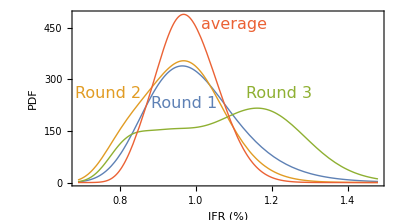

brazil-ifr-plot-marg-40-80days-new.pdf

```mathematica
colors=ColorData[97,"ColorList"];
pifr=Plot[{ifrfun1[x/100],ifrfun2[x/100],ifrfun3[x/100],ifr123[x/100]},{x,.69,1.48},Frame->True,FrameStyle->16,FrameLabel->{"IFR (%)","PDF"},PlotRange->All,PlotStyle->Thick,AspectRatio->.55];
sifr=Show[pifr,
Graphics[Text[Style["Round 1",16,colors[[1]]],{.97,230}]],Graphics[Text[Style["Round 2",16,colors[[2]]],{.77,260}]],Graphics[Text[Style["Round 3",16,colors[[3]]],{1.22,260}]],Graphics[Text[Style["average",16,colors[[4]]],{1.1,460}]]]
Export["brazil-ifr-plot-marg-40-80days-new.pdf",sifr]
```

```mathematica
Dimensions[ifrmargTroundtab]
(*Export["ifrmargTroundtab.tab",ifrmargTroundtab,"List"];*)
```

{1}

```mathematica
ifrmargTroundtab[[3]]
```

-33.4448 InterpolatingFunction[…][x]

```mathematica
Monitor[ifrCImargTcombined=Table[
f[x_]=ifrmargTroundtab[[agebin]];
{ifrmin,ifrmax}={.003,.02};
If[agebin==2,{ifrmin,ifrmax}={1.5 10.^-4,.0006}];
If[agebin==3,{ifrmin,ifrmax}={.001,.004}];If[agebin==5,{ifrmin,ifrmax}={.02,.05}];
ifrcountry[f,ifrmin,ifrmax]
,{agebin,5}],agebin]
Round[100 ifrCImargTcombined,.01]
```

Part::partw: Part 2 of {14.6345 InterpolatingFunction[{{0.,0.9}},{5,7,0,{754},{4},0,0,0,0,Automatic,«3»},{{0.,1.×10^-6,3.×10^-6,0.0001,0.00014,0.00018,0.00022,0.00026,0.0003,0.00034,«744»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«745»},{0.,0.,0.,-0.144,-0.144,-0.144,-0.144,-0.144,-0.144,-0.144,«744»}},{Automatic}][x]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NMaximize::nnum: The function value -{-2.10737}⟦2⟧ is not a number at {x} = {0.000170579}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

ReplaceAll::reps: {x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::srect: Value 0.9 (x/.x) in search specification {x,(9 xxmax)/10,0.00015,xxmax} is not a number or array of numbers.

FindRoot::srect: Value 1.1 (x/.x) in search specification {x,(11 xxmax)/10,xxmax,0.0006} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

NIntegrate::nlim: x = x/.FindRoot[f[x]==zrange⟦j⟧,{x,(9 xxmax)/10,0.00015,xxmax}] is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

Interpolation::indat: Data point {{({14.6345 InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][x]}⟦2⟧)/1000,(13 {14.6345 InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][x]}⟦2⟧)/3000,(23 {14.6345 InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][x]}⟦2⟧)/3000,(11 {14.6345 «21»[«1»][x]}⟦2⟧)/1000,(43 {«1»}⟦2⟧)/3000,(«1»)/3000,(21 «1»)/1000,(73 {«1»}⟦2⟧)/3000,(83 {14.6345 InterpolatingFunction[{«1»},«3»,{«1»}][x]}⟦2⟧)/3000,(31 {14.6345 InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][x]}⟦2⟧)/1000,«90»},«1»} contains abscissa {({14.6345 InterpolatingFunction[{{«2»}},{5,7,0,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«754»}},{Developer`PackedArrayForm,{«755»},{«754»}},{Automatic}][x]}⟦2⟧)/1000,(13 {14.6345 InterpolatingFunction[{{«2»}},{5,7,0,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«754»}},{Developer`PackedArrayForm,{«755»},{«754»}},{Automatic}][x]}⟦2⟧)/3000,(23 {14.6345 InterpolatingFunction[«1»][x]}⟦2⟧)/3000,(11 {«19» «1»}⟦2⟧)/1000,(«1»)/3000,«1»,«1»,(73 «1»)/3000,(83 {14.6345 «1»[x]}⟦2⟧)/3000,(31 {14.6345 «1»[x]}⟦2⟧)/1000,«90»}, which is not a real number.

NMinimize::bcons: The following constraints are not valid: {0.00015<x,x<(x/.x)}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

NMinimize::bcons: The following constraints are not valid: {x<0.0006,(x/.x)<x}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Interpolation::indat: Data point {{({14.6345 InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][x]}⟦3⟧)/1000,(13 {14.6345 InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][x]}⟦3⟧)/3000,(23 {14.6345 InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][x]}⟦3⟧)/3000,(11 {14.6345 «21»[«1»][x]}⟦3⟧)/1000,(43 {«1»}⟦3⟧)/3000,(«1»)/3000,(21 «1»)/1000,(73 {«1»}⟦3⟧)/3000,(83 {14.6345 InterpolatingFunction[{«1»},«3»,{«1»}][x]}⟦3⟧)/3000,(31 {14.6345 InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][x]}⟦3⟧)/1000,«90»},«1»} contains abscissa {({14.6345 InterpolatingFunction[{{«2»}},{5,7,0,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«754»}},{Developer`PackedArrayForm,{«755»},{«754»}},{Automatic}][x]}⟦3⟧)/1000,(13 {14.6345 InterpolatingFunction[{{«2»}},{5,7,0,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«754»}},{Developer`PackedArrayForm,{«755»},{«754»}},{Automatic}][x]}⟦3⟧)/3000,(23 {14.6345 InterpolatingFunction[«1»][x]}⟦3⟧)/3000,(11 {«19» «1»}⟦3⟧)/1000,(«1»)/3000,«1»,«1»,(73 «1»)/3000,(83 {14.6345 «1»[x]}⟦3⟧)/3000,(31 {14.6345 «1»[x]}⟦3⟧)/1000,«90»}, which is not a real number.

General::stop: Further output of Interpolation::indat will be suppressed during this calculation.

NMinimize::bcons: The following constraints are not valid: {0.001<x,x<(x/.x)}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

General::stop: Further output of NMinimize::bcons will be suppressed during this calculation.

{{0.00984534,0.00821416,0.0122112,0.95},{x/.x,x/.x,x/.x,0.},{x/.x,x/.x,x/.x,0.},{x/.x,x/.x,x/.x,0.},{x/.x,x/.x,x/.x,0.}}

{{0.98,0.82,1.22,95.},{Round[100 (x/.x),0.01],Round[100 (x/.x),0.01],Round[100 (x/.x),0.01],0.},{Round[100 (x/.x),0.01],Round[100 (x/.x),0.01],Round[100 (x/.x),0.01],0.},{Round[100 (x/.x),0.01],Round[100 (x/.x),0.01],Round[100 (x/.x),0.01],0.},{Round[100 (x/.x),0.01],Round[100 (x/.x),0.01],Round[100 (x/.x),0.01],0.}}

```mathematica
Round[100 ifrCImargTcombined,.1]
```

{{1.,0.8,1.2,95.},{Round[100 (x/.x),0.1],Round[100 (x/.x),0.1],Round[100 (x/.x),0.1],0.},{Round[100 (x/.x),0.1],Round[100 (x/.x),0.1],Round[100 (x/.x),0.1],0.},{Round[100 (x/.x),0.1],Round[100 (x/.x),0.1],Round[100 (x/.x),0.1],0.},{Round[100 (x/.x),0.1],Round[100 (x/.x),0.1],Round[100 (x/.x),0.1],0.}}

```mathematica
Monitor[ifrCImargT=Table[
f[x_]=ifrmargTtab[[agebin,round]];
{ifrmin,ifrmax}={.005,.023};
If[agebin==2,{ifrmin,ifrmax}={0.7 10.^-4,.0008}];
If[agebin==3,{ifrmin,ifrmax}={.0008,.005}];If[agebin==5,{ifrmin,ifrmax}={.01,.07}];
ifrcountry[f,ifrmin,ifrmax]
,{agebin,5},{round,1,3}];,{agebin,round}]
Round[100 ifrCImargT,.001]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {0.07} is at the edge of the search region {0.0304839,0.07} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.07} is at the edge of the search region {0.0407981,0.07} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

{{{0.965,0.773,1.257,95.},{0.968,0.746,1.168,95.},{1.162,0.76,1.373,95.}},{{0.022,0.017,0.031,95.},{0.034,0.025,0.046,95.},{0.039,0.023,0.052,95.}},{{0.198,0.153,0.274,95.},{0.211,0.152,0.268,95.},{0.292,0.174,0.37,95.}},{{0.96,0.756,1.286,95.},{1.218,0.881,1.647,95.},{1.224,0.764,1.609,95.}},{{2.289,1.764,3.199,95.},{3.048,2.182,4.601,95.},{4.08,2.701,5.86,95.}}}

```mathematica
Round[100 ifrCImargT,.01]
```

{{{0.96,0.77,1.26,95.},{0.97,0.75,1.17,95.},{1.16,0.76,1.37,95.}},{{0.02,0.02,0.03,95.},{0.03,0.02,0.05,95.},{0.04,0.02,0.05,95.}},{{0.2,0.15,0.27,95.},{0.21,0.15,0.27,95.},{0.29,0.17,0.37,95.}},{{0.96,0.76,1.29,95.},{1.22,0.88,1.65,95.},{1.22,0.76,1.61,95.}},{{2.29,1.76,3.2,95.},{3.05,2.18,4.6,95.},{4.08,2.7,5.86,95.}}}

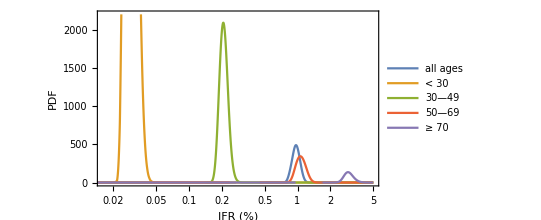

```mathematica
ticksvec=Join[{.03,.1,.3,1,3},Table[{i,""},{i,.01,.09,.01}],Table[{i,""},{i,.1,.9,.1}],Table[{i,""},{i,1,9}]];
ticksvectop=Join[Table[{i,""},{i,.01,.09,.01}],Table[{i,""},{i,.1,.9,.1}],Table[{i,""},{i,1,9}]];
fticks={{Automatic,Automatic},{ticksvec,None}};
pdfmargplot=LogLinearPlot[Evaluate[ifrmargTroundtab/.x->y/100],{y,1. 10.^-2,5},PlotRange->{{1.6 10.^-2,5},{0,2200}},Frame->True,FrameStyle->16,FrameLabel->{"IFR (%)","PDF"},
FrameTicks->fticks,PlotStyle->Thick,PlotLegends->Placed[{"all ages ","< 30 ","30—49 ","50—69 ","≥ 70"},Top],AspectRatio->.55]
```

### IFR Imperial Brazil Report 21

```mathematica
(* Estimates for 6/May/2020 *)
```

```mathematica
imperialstates={"SP","RJ","CE","PE","AM","PA","MA","BA","ES","PR","MG","PB","AL","RS","RN","SC"}
imperialpop={46.3,17.4,9.2,9.6,4.2,8.7,7.1,14.9,3.1,11.5,21.3,4.0,3.4,11.3,3.5,7.3};
imperialIFR=.1{7,8,11,11,8,9,10,11,9,9,10,12,11,9,11,8};
imperialIFR.imperialpop/Total[imperialpop]
```

{SP,RJ,CE,PE,AM,PA,MA,BA,ES,PR,MG,PB,AL,RS,RN,SC}

0.900055

```mathematica
imperial=Thread[{imperialstates,imperialIFR}]
imperial=Sort[imperial]
k=1;
imperiallist=Reap[Table[If[statesnames[[i]]==imperial[[k,1]],Sow[{i,imperialIFR[[k]]}];k=Min[k+1,Length[imperial]];]
,{i,27}]][[2,1]]
```

{{SP,0.7},{RJ,0.8},{CE,1.1},{PE,1.1},{AM,0.8},{PA,0.9},{MA,1.},{BA,1.1},{ES,0.9},{PR,0.9},{MG,1.},{PB,1.2},{AL,1.1},{RS,0.9},{RN,1.1},{SC,0.8}}

{{AL,1.1},{AM,0.8},{BA,1.1},{CE,1.1},{ES,0.9},{MA,1.},{MG,1.},{PA,0.9},{PB,1.2},{PE,1.1},{PR,0.9},{RJ,0.8},{RN,1.1},{RS,0.9},{SC,0.8},{SP,0.7}}

{{2,0.7},{3,0.8},{5,1.1},{6,1.1},{8,0.8},{10,0.9},{11,1.},{14,1.1},{15,0.9},{16,0.9},{18,1.},{19,1.2},{20,1.1},{23,0.9},{24,1.1},{26,0.8}}

### IFR Plot

```mathematica
dirIFR2="tables\\";
ϵ=.2;
```

```mathematica
data1=Import[dirIFR<>"IFR-95CI-MQ-round1-40-80days-v6a.txt","CSV"][[All,2;;]];
IFRstatesRound1=Thread[{Range[1,27]-ϵ,errorfun[data1]}];
data2=Import[dirIFR<>"IFR-95CI-MQ-round2-40-80days-v6a.txt","CSV"][[All,2;;]];
IFRstatesRound2=Thread[{Range[1,27],errorfun[data2]}];
data3=Import[dirIFR<>"IFR-95CI-MQ-round3-40-80days-v6a.txt","CSV"][[All,2;;]];
IFRstatesRound3=Thread[{Range[1,27]+ϵ,errorfun[data3]}];
data123=Import[dirIFR<>"IFR-95CI-MQ-combined-40-80days-v6a.txt","CSV"][[All,2;;]];
IFRstatescombined=Thread[{Range[1,27],errorfun[data123]}];
ifrBRfit=0.0097*100;
```

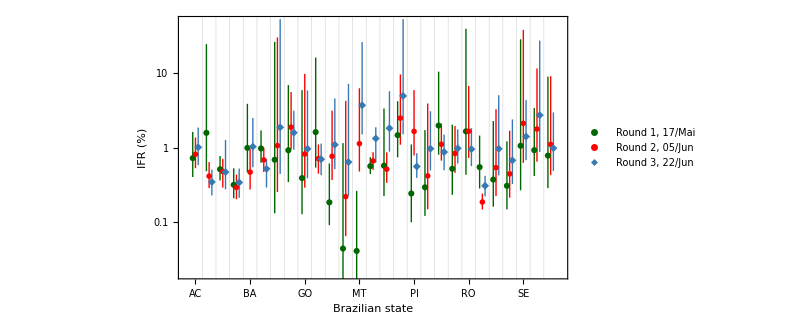

```mathematica
lpstatesIFRENlog=ListLogPlot[{IFRstatesRound1,IFRstatesRound2,IFRstatesRound3(*,IFRstatescombined*)},Frame->True,ImageSize->600,PlotRange->{{.3,27.7},{.02,50}},FrameStyle->24,FrameLabel->{"Brazilian state","IFR  (%)"},PlotStyle->{Darker[Green,.6],Red,color1,Black},
IntervalMarkersStyle->{Darker[Green,.6],Red,color1,Black},PlotMarkers->{Automatic,"OpenMarkers",Automatic,Automatic},FrameTicks->{{Join[Table[{i,""},{i,.005,.01,.001}],Table[{i,""},{i,.01,.1,.01}],Table[{i,""},{i,.1,1,.1}],Table[{i,""},{i,1,10,1}],Table[{i,""},{i,10,100,10}],{.01,.1,1,10}],
Join[Table[{i,""},{i,.01,.1,.01}],Table[{i,""},{i,.1,1,.1}],Table[{i,""},{i,1,10,1}],Table[{i,""},{i,10,100,10}]]},{Table[{i,If[OddQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}],Table[{i,If[EvenQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}]}},FrameTicksStyle->22,AspectRatio->.55,PlotLegends->Placed[{Style["Round 1, 17/Mai",20],Style["Round 2, 05/Jun",20],Style["Round 3, 22/Jun",20]},{.498,.82}],
GridLines->{Range[1.5,26.5,1],None},GridLinesStyle->Lighter[Gray,.7]]
```

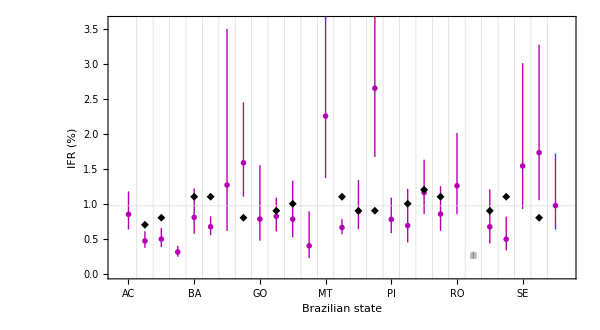

```mathematica
lpstatesIFRcombinedimperial=ListPlot[{IFRstatescombined[[Delete[Range[1,27],{{22}}]]],IFRstatescombined[[{22}]],imperiallist},Frame->True,ImageSize->600,PlotRange->{{.3,27.7},{0,3.6}},FrameStyle->24,FrameLabel->{"Brazilian state","IFR  (%)"},PlotStyle->{Darker[Magenta,.3],Opacity[.3,Gray],Black},
IntervalMarkersStyle->{Darker[Magenta,.3],Opacity[.8,Gray]},PlotMarkers->{"OpenMarkers",Automatic,Automatic},FrameTicks->{{Automatic,Automatic},{Table[{i,If[OddQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}],Table[{i,If[EvenQ[i],Style[statesnames[[i]],24,FontFamily->"Economica"],""]},{i,Length[statesnames]}]}},
FrameTicksStyle->22,AspectRatio->.55,(*PlotLegends->Placed[{Style["Round 1, 17/Mai",20],Style["Round 2, 05/Jun",20],Style["Round 3, 22/Jun",20]},{.498,.82}],*)
GridLines->{Range[1.5,26.5,1],{ifrBRfit}},GridLinesStyle->{Lighter[Gray,.7],Red}]
```